C:\Users\liupe\Desktop\biduffing\Code\bistable_para_duffing_x

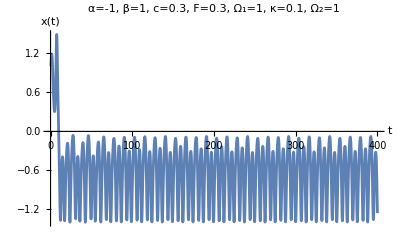

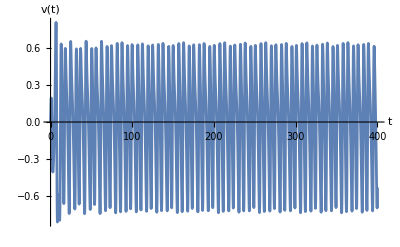

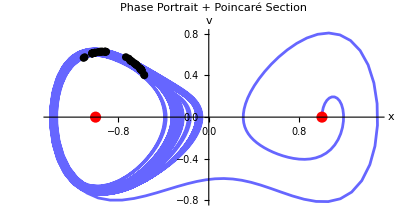

```mathematica
SetDirectory@NotebookDirectory[]
ClearAll[FindStableEq,IntegrateAndPlotForced];

(*仅用于给初值定位左右井的"参考静平衡"（只看 F0，不含 Cos 项）*)
FindStableEq[α_,β_,F0_]:=Module[{xs},xs=x/. NSolve[β x^3+α x-F0==0,x,Reals];
Sort@Select[xs,(α+3 β #^2)>0&]];

(*修改后的函数：增加参数激励项 κ x cos(Ω₂ t)*)
IntegrateAndPlotForced[α_:-1,β_:1,c_:0.3,F_:0.3,Ω1_:1,κ_:0.1,Ω2_:1,tmax_:400.,dt_:0.001,ic_:Automatic,tSettle_:20.]:=Module[{stables,x0,v0,xFun,vFun,t,T,tgrid,xPlot,vPlot,phasePlot,eqPts,eqOverlay,poincT0,nP,poincPts,poincPlot},(*参考平衡点（无激励时，F=0,κ=0）*)stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["未找到两个稳定平衡（参考 F0=0）。请检查 α<0, β>0。"];
Return[$Failed]];
{x0,v0}=If[ic===Automatic,{stables[[2]],0.0},ic];
T=2 Pi/Ω1;(*主激励周期*)Clear[x,v,t];
(*修改的运动方程：添加参数激励项*){xFun,vFun}=NDSolveValue[{x'[t]==v[t],v'[t]==-c v[t]-α x[t]-β x[t]^3+F Cos[Ω1 t]+κ x[t] Cos[Ω2 t],x[0]==x0,v[0]==v0},{x,v},{t,0,tmax},Method->"ExplicitRungeKutta"];
tgrid=N@Range[0,tmax,dt];
(*时间历程图*)xPlot=Plot[xFun[t],{t,0,tmax},AxesLabel->{"t","x(t)"},PlotRange->All,PlotLabel->StringForm["α=``, β=``, c=``, F=``, Ω₁=``, κ=``, Ω₂=``",α,β,c,F,Ω1,κ,Ω2]];
vPlot=Plot[vFun[t],{t,0,tmax},AxesLabel->{"t","v(t)"},PlotRange->All];
(*相图*)phasePlot=ParametricPlot[{xFun[t],vFun[t]},{t,0,tmax},AxesLabel->{"x","v"},PlotRange->All,PlotStyle->Directive[Opacity[0.6],Blue]];
(*参考平衡点标记*)eqPts=Thread[{stables,0}];
eqOverlay=Graphics[{Red,PointSize[0.02],Point[eqPts]}];
(*Poincaré 截面采样（去掉过渡段）*)poincT0=Max[tSettle,5 T];
nP=Floor[(tmax-poincT0)/T];
poincPts=Table[{xFun[poincT0+k T],vFun[poincT0+k T]},{k,0,nP}];
poincPlot=ListPlot[poincPts,PlotStyle->Black,PlotMarkers->{Automatic,8}];
Print@xPlot;
Print@vPlot;
Show[phasePlot,eqOverlay,poincPlot,PlotLabel->"Phase Portrait + Poincaré Section"]];

(*默认调用*)
IntegrateAndPlotForced[]
```

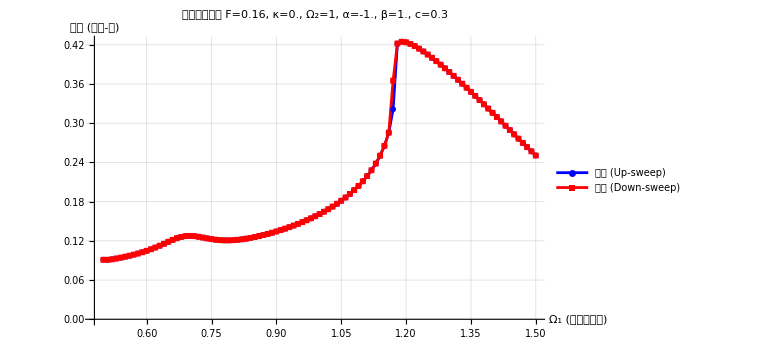

```mathematica
ClearAll[FRFSweep,PlotFRF];

(*修改后的FRF扫描：适配参数激励*)
FRFSweep[α_:-1.,β_:1.,c_:0.3,F_:0.16,Ω1min_:0.5,Ω1max_:1.5,dΩ1_:0.01,κ_:0.0,Ω2_:1,(*新增：参数激励参数*)cyclesSettle_:60,cyclesMeasure_:20,dt_:0.001,ic_:Automatic]:=Module[{stables,ic0,doOne,forwardGrid,backwardGrid,state,res,forward,backward},(*参考平衡点（无激励时）*)stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["未找到两个稳定平衡（参考 F=0）。请检查 α<0, β>0。"];
Return[$Failed]];
ic0=If[ic===Automatic,{stables[[2]],0.0},ic];
(*单个频率点的计算*)doOne[Ω1_,{x0_,v0_}]:=Module[{T=2 Pi/Ω1,tS,tM,xFun,vFun,ts,xs,xmax,xmin,amp,rms,last},tS=cyclesSettle*T;
tM=cyclesMeasure*T;
Clear[x,v,t];
(*修改的运动方程：包含参数激励*){xFun,vFun}=NDSolveValue[{x'[t]==v[t],v'[t]==-c v[t]-α x[t]-β x[t]^3+F Cos[Ω1 t]+κ x[t] Cos[Ω2 t],x[0]==x0,v[0]==v0},{x,v},{t,0,tS+tM},Method->"ExplicitRungeKutta",MaxStepFraction->0.1];
ts=Range[tS,tS+tM,dt];
xs=xFun/@ts;
xmax=Max[xs];
xmin=Min[xs];
amp=(xmax-xmin)/2.;
rms=Sqrt[Mean[(xs-Mean[xs])^2]];
last={xFun[tS+tM],vFun[tS+tM]};
<|"Omega1"->Ω1,"Amp"->amp,"xmax"->xmax,"xmin"->xmin,"RMS"->rms,"xend"->last[[1]],"vend"->last[[2]]|>];
(*前扫：从低频到高频*)forwardGrid=Range[Ω1min,Ω1max,dΩ1];
state=ic0;
forward=Table[res=doOne[Ω1,state];
state={res["xend"],res["vend"]};
KeyDrop[res,{"xend","vend"}],{Ω1,forwardGrid}];
(*后扫：从高频到低频*)backwardGrid=Range[Ω1max,Ω1min,-dΩ1];
state=ic0;
res=doOne[Ω1max,state];
state={res["xend"],res["vend"]};
backward=Table[res=doOne[Ω1,state];
state={res["xend"],res["vend"]};
KeyDrop[res,{"xend","vend"}],{Ω1,backwardGrid}];
<|"forward"->forward,"backward"->backward,"params"-><|"κ"->κ,"Ω2"->Ω2,"F"->F,"α"->α,"β"->β,"c"->c|>|>];

(*绘制FRF曲线*)
PlotFRF[frf_Association]:=Module[{dataF,dataB,params},dataF=Values/@(frf["forward"][[All,{"Omega1","Amp"}]]);
dataB=Values/@(frf["backward"][[All,{"Omega1","Amp"}]]);
params=frf["params"];
ListLinePlot[{dataF,dataB},PlotLegends->{"前扫 (Up-sweep)","后扫 (Down-sweep)"},PlotMarkers->{Automatic,6},AxesLabel->{"Ω₁ (外激励频率)","幅值 (半峰-峰)"},GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->StringForm["频率响应曲线\nF=``, κ=``, Ω₂=``, α=``, β=``, c=``",params["F"],params["κ"],params["Ω2"],params["α"],params["β"],params["c"]],PlotStyle->{Blue,Red}]];

(*示例调用*)
(*基础调用（使用默认参数）*)frf=FRFSweep[];
PlotFRF[frf]
```

调试信息：

Sweep Type: Omega2

Params: <|κ→0.25,Ω1→1.,F→0,α→-1.,β→1.,c→0.3|>

使用的频率变量: Omega2

Forward 数据范围: {0.5,1.5}

Backward 数据范围: {0.5,1.5}

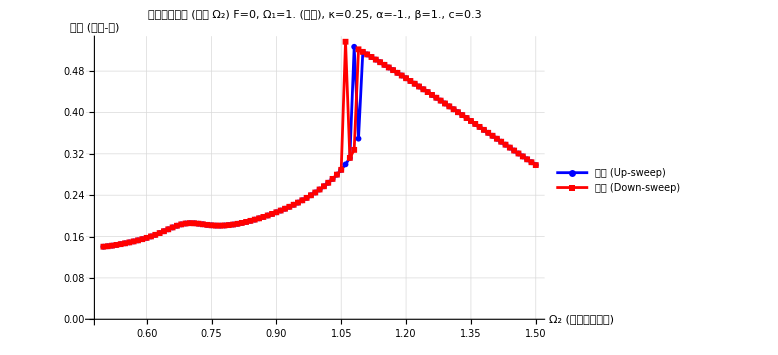

```mathematica
(*新函数：扫描参数激励频率 Ω₂，固定 Ω₁*)FRFSweepParametric[α_:-1.,β_:1.,c_:0.3,F_:0,Ω1_:1.0,κ_:0.25,Ω2min_:0.5,Ω2max_:1.5,dΩ2_:0.01,cyclesSettle_:60,cyclesMeasure_:20,dt_:0.001,ic_:Automatic]:=Module[{stables,ic0,doOne,forwardGrid,backwardGrid,state,res,forward,backward},stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["未找到两个稳定平衡（参考 F=0）。请检查 α<0, β>0。"];
Return[$Failed]];
ic0=If[ic===Automatic,{stables[[2]],0.0},ic];
(*单个频率点的计算-扫描 Ω₂*)doOne[Ω2_,{x0_,v0_}]:=Module[{T1,T2,Tbase,tS,tM,xFun,vFun,ts,xs,xmax,xmin,amp,rms,last},(*两个激励的周期*)T1=2 Pi/Ω1;
T2=2 Pi/Ω2;
(*选择合适的基础周期用于稳定和测量 可以选择：1. 用 T1（外激励周期） 2. 用两个周期的最小公倍数（如果频率比是有理数） 3. 用较小的周期 这里我们用 T1 作为参考*)Tbase=T1;
tS=cyclesSettle*Tbase;
tM=cyclesMeasure*Tbase;
Clear[x,v,t];
{xFun,vFun}=NDSolveValue[{x'[t]==v[t],v'[t]==-c v[t]-α x[t]-β x[t]^3+F Cos[Ω1 t]+κ x[t] Cos[Ω2 t],(*这里 Ω2 是变化的*)x[0]==x0,v[0]==v0},{x,v},{t,0,tS+tM},Method->"ExplicitRungeKutta",MaxStepFraction->0.1];
ts=Range[tS,tS+tM,dt];
xs=xFun/@ts;
xmax=Max[xs];
xmin=Min[xs];
amp=(xmax-xmin)/2.;
rms=Sqrt[Mean[(xs-Mean[xs])^2]];
last={xFun[tS+tM],vFun[tS+tM]};
<|"Omega1"->Ω1,"Omega2"->Ω2,"Amp"->amp,"xmax"->xmax,"xmin"->xmin,"RMS"->rms,"xend"->last[[1]],"vend"->last[[2]]|>];
(*前扫：从低频到高频-扫描 Ω₂*)forwardGrid=Range[Ω2min,Ω2max,dΩ2];
state=ic0;
forward=Table[res=doOne[Ω2,state];(*注意这里传入的是 Ω2*)state={res["xend"],res["vend"]};
KeyDrop[res,{"xend","vend"}],{Ω2,forwardGrid}];(*循环变量是 Ω2*)(*后扫：从高频到低频-扫描 Ω₂*)backwardGrid=Range[Ω2max,Ω2min,-dΩ2];
state=ic0;
res=doOne[Ω2max,state];
state={res["xend"],res["vend"]};
backward=Table[res=doOne[Ω2,state];(*注意这里传入的是 Ω2*)state={res["xend"],res["vend"]};
KeyDrop[res,{"xend","vend"}],{Ω2,backwardGrid}];(*循环变量是 Ω2*)<|"forward"->forward,"backward"->backward,"sweepType"->"Omega2","params"-><|"κ"->κ,"Ω1"->Ω1,"F"->F,"α"->α,"β"->β,"c"->c|>|>];
PlotFRF[frf_Association]:=Module[{dataF,dataB,params,sweepType,xLabel,titleStr,sweepVar},sweepType=frf["sweepType"];
params=frf["params"];
Print["调试信息："];
Print["  Sweep Type: ",sweepType];
Print["  Params: ",params];
(*根据扫描类型选择要绘制的频率变量*)If[sweepType==="Omega1",sweepVar="Omega1";
xLabel="Ω₁ (外激励频率)";
titleStr=StringForm["频率响应曲线 (扫描 Ω₁)\nF=``, κ=``, Ω₂=`` (固定), α=``, β=``, c=``",params["F"],params["κ"],params["Ω2"],params["α"],params["β"],params["c"]],(*else*)sweepVar="Omega2";
xLabel="Ω₂ (参数激励频率)";
titleStr=StringForm["频率响应曲线 (扫描 Ω₂)\nF=``, Ω₁=`` (固定), κ=``, α=``, β=``, c=``",params["F"],params["Ω1"],params["κ"],params["α"],params["β"],params["c"]]];
Print["  使用的频率变量: ",sweepVar];
(*提取数据*)dataF=Values/@(frf["forward"][[All,{sweepVar,"Amp"}]]);
dataB=Values/@(frf["backward"][[All,{sweepVar,"Amp"}]]);
Print["  Forward 数据范围: ",MinMax[dataF[[All,1]]]];
Print["  Backward 数据范围: ",MinMax[dataB[[All,1]]]];
ListLinePlot[{dataF,dataB},PlotLegends->{"前扫 (Up-sweep)","后扫 (Down-sweep)"},PlotMarkers->{Automatic,6},AxesLabel->{xLabel,"幅值 (半峰-峰)"},GridLines->Automatic,ImageSize->Large,PlotRange->All,PlotLabel->titleStr,PlotStyle->{Blue,Red}]];
(*测试扫描 Ω₂*)frf2=FRFSweepParametric[];
PlotFRF[frf2]
```

数据生成配置：

方程: x'' + c*x' + α*x + β*x.b3 = κ*x*cos(Ω*t)

频率 Ω: 21 点 [0.080 ~ 0.239 Hz]

幅值 κ: 13 点 {0,0.1,0.2,0.25,0.26,0.27,0.28,0.29,0.3,1,2,3,5}

总组合: 273

初值: x₀ ∈ {-1.00, 1.00}

进度: 20/273

进度: 40/273

进度: 60/273

进度: 80/273

进度: 100/273

进度: 120/273

进度: 140/273

进度: 160/273

进度: 180/273

进度: 200/273

进度: 220/273

进度: 240/273

进度: 260/273

进度: 273/273

数据抽样完成：

训练集: 873655 样本

验证集: 218400 样本

测试集: 218400 样本

统计信息：

输入 [x, v, κ*cos(Ωt), κ*sin(Ωt)]: μ = {-0.00,0.00,0.00,-0.00}, σ = {1.05,0.70,1.23,1.23}

输出 [ga]: μ = -0.001, σ = 1.313

✅ 数据已保存

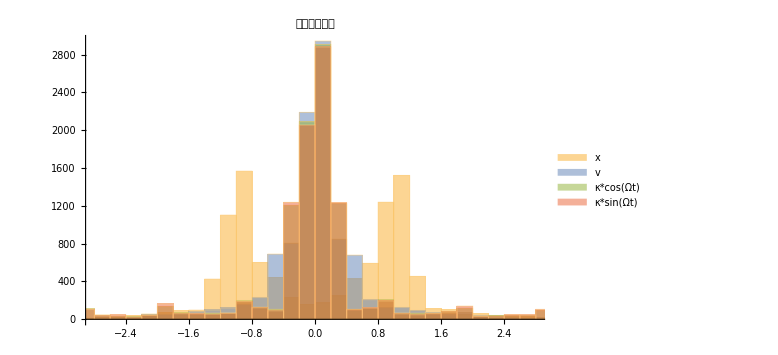

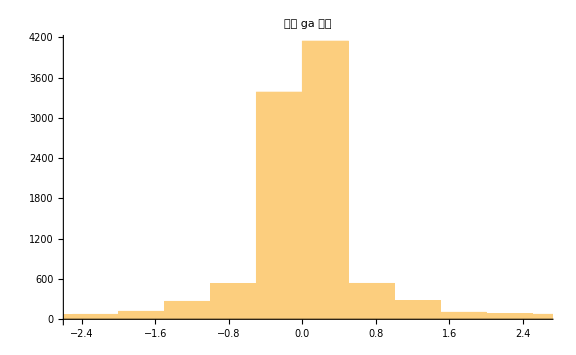

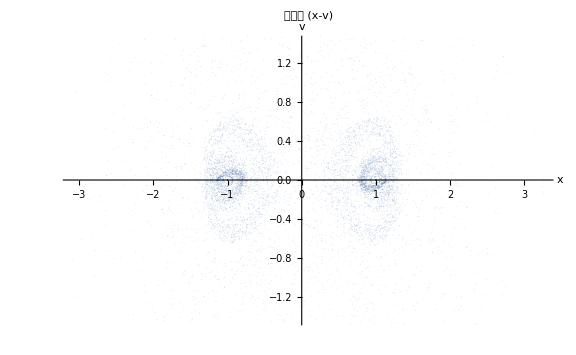

✅ 完成

```mathematica
(* ==================Duffing 参数激励振动：多激励幅值+分层采样==================*)(*方程：x''+c*x'+α*x+β*x.b3=κ*x*Cos[Ω*t]*)(*目标：神经网络学习 ga=-c*v-α*x-β*x.b3+κ*x*cos(Ω*t)*)ClearAll[α,β,c,FindStableEq,GenerateDataFromInitial,freqList,kappaList,allTrainData,allValData,allTestData,trainData,valData,testData,allInputs,allTargets,inputMean,inputStd,targetMeanGa,targetStdGa];

(*----------物理参数（双稳）----------*)
α=-1.;
β=1.;
c=0.3;

(*----------计算两个稳定静平衡----------*)
FindStableEq[α_,β_]:=Module[{xs},xs=x/. NSolve[β*x^3+α*x==0,x,Reals];
Sort@Select[xs,(α+3*β*#^2)>0&]];

stables=FindStableEq[α,β];
If[Length[stables]<2,Print["❌ 未找到两个稳定平衡，请检查参数。"];
Abort[];];

orix1=stables[[1]];
orix2=stables[[2]];

(*----------从一个初值生成数据----------*)
GenerateDataFromInitial[freq_,kappa_,orix_]:=Module[{Ω,tEnd,h,tgrid,xFun,vFun,xvals,vvals,kappaCos,kappaSin,data,list},Ω=freq*2*π;
tEnd=100./freq;
h=1./(200.*freq);
tgrid=N@Range[0,tEnd,h];
Clear[x,v,t];
{xFun,vFun}=NDSolveValue[{x'[t]==v[t],v'[t]==-c*v[t]-α*x[t]-β*x[t]^3+kappa*x[t]*Cos[Ω*t],x[0]==orix,v[0]==0.},{x,v},{t,0,tEnd},MaxStepSize->h/2];
xvals=xFun/@tgrid;
vvals=vFun/@tgrid;
kappaCos=kappa*Cos[Ω*tgrid];
kappaSin=kappa*Sin[Ω*tgrid];
data=Transpose[{xvals,vvals,kappaCos,kappaSin}];
list=Table[With[{xvks=data[[i]],xval=xvals[[i]],vval=vvals[[i]],kc=kappaCos[[i]]},Module[{ga},ga=(-c*vval-α*xval-β*xval^3+kc*xval);
xvks->{ga}]],{i,Length[tgrid]}];
list];

(* ==================分层采样配置==================*)
freqList=Range[0.5,1.5,0.05]/2/π;  (*参数激励频率范围*)
kappaList={0,0.1,0.2,0.25,0.26,0.27,0.28,0.29,0.3,1,2,3,5};  (*参数激励幅值*)

Print["数据生成配置："];
Print["  方程: x'' + c*x' + α*x + β*x.b3 = κ*x*cos(Ω*t)"];
Print["  频率 Ω: ",Length[freqList]," 点 [",NumberForm[freqList[[1]],{4,3}]," ~ ",NumberForm[freqList[[-1]],{4,3}]," Hz]"];
Print["  幅值 κ: ",Length[kappaList]," 点 ",kappaList];
Print["  总组合: ",Length[freqList]*Length[kappaList]];
Print["  初值: x₀ ∈ {",NumberForm[orix1,{4,2}],", ",NumberForm[orix2,{4,2}],"}"];

allTrainData={};
allValData={};
allTestData={}; (*增加测试集数据*)
totalCombinations=Length[freqList]*Length[kappaList];
currentCombination=0;

Do[Do[Module[{samples1,samples2,allSamplesCombo,shuffled,splitIdx},currentCombination++;
If[Mod[currentCombination,20]==0||currentCombination==totalCombinations,Print["  进度: ",currentCombination,"/",totalCombinations];];
samples1=GenerateDataFromInitial[freq,kappa,orix1];
samples2=GenerateDataFromInitial[freq,kappa,orix2];
allSamplesCombo=Join[samples1,samples2];
shuffled=RandomSample[allSamplesCombo];
splitIdx=Round[0.8*Length[shuffled]];
allTrainData=Join[allTrainData,shuffled[[1;;splitIdx]]];
allValData=Join[allValData,shuffled[[splitIdx+1;;-1]]];],{kappa,kappaList}],{freq,freqList}];

allTrainData=RandomSample[allTrainData];
allValData=RandomSample[allValData];

(* ==================随机抽取 10%==================*)
samplingRatio=0.1;
trainSize=Round[Length[allTrainData]*samplingRatio];
valSize=Round[Length[allValData]*samplingRatio];
testSize=Round[Length[allValData]*samplingRatio]; (*测试集大小也设定为10%*)
trainData=RandomSample[allTrainData,trainSize];
valData=RandomSample[allValData,valSize];
testData=RandomSample[allValData,testSize]; (*从验证集中抽取10%作为测试集*)

Print["数据抽样完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];

(* ==================数据统计==================*)
allInputs=trainData[[All,1]];
allTargets=trainData[[All,2]];

inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs];
targetMeanGa=Mean[allTargets[[All,1]]];
targetStdGa=StandardDeviation[allTargets[[All,1]]];

Print["统计信息："];
Print["  输入 [x, v, κ*cos(Ωt), κ*sin(Ωt)]: μ = ",NumberForm[inputMean,{4,2}],", σ = ",NumberForm[inputStd,{4,2}]];
Print["  输出 [ga]: μ = ",NumberForm[targetMeanGa,{6,3}],", σ = ",NumberForm[targetStdGa,{6,3}]];

(* ==================保存数据==================*)
Export[FileNameJoin[{Directory[],"trainData_parametric_duffing.mx"}],trainData,"MX"];
Export[FileNameJoin[{Directory[],"valData_parametric_duffing.mx"}],valData,"MX"];
Export[FileNameJoin[{Directory[],"testData_parametric_duffing.mx"}],testData,"MX"]; (*保存测试集*)

normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMeanGa"->targetMeanGa,"targetStdGa"->targetStdGa,"freqList"->freqList,"kappaList"->kappaList,"alpha"->α,"beta"->β,"damping"->c|>;

Export[FileNameJoin[{Directory[],"normParams_parametric.mx"}],normParams,"MX"];

Print["✅ 数据已保存"];

(* ==================可视化==================*)
sampleSize=Min[10000,Length[trainData]];
sampledData=RandomSample[trainData,sampleSize];
sampledInputs=sampledData[[All,1]];
sampledTargets=sampledData[[All,2,1]];

fig1=Histogram[Transpose[sampledInputs],30,PlotLabel->"输入特征分布",ChartLegends->{"x","v","κ*cos(Ωt)","κ*sin(Ωt)"},ImageSize->Large];

fig2=Histogram[sampledTargets,50,PlotLabel->"输出 ga 分布",ImageSize->Large];

fig3=ListPlot[sampledInputs[[All,{1,2}]],PlotStyle->{PointSize[0.001],Opacity[0.3]},AxesLabel->{"x","v"},PlotLabel->"相空间 (x-v)",ImageSize->Large];

Print@fig1;
Print@fig2;
Print@fig3;
sampledInputsForExcel=sampledInputs[[All,{1,2}]];  (*选择x和v的数据*)

(*将数据导出到Excel文件*)
Export[FileNameJoin[{Directory[],"phase_space_x_v.xlsx"}],sampledInputsForExcel,"XLSX"];

Print["✅ 完成"];
```

数据加载完成：

训练集: 873655 样本

验证集: 218400 样本

测试集: 218400 样本

总计: 1310455 样本

输入维度: 4, 输出维度: 1

开始多阶段训练...

========== Stage 1 : rounds=200, lr=0.0005 ==========

验证集评估：

RMSE = {0.0021}

Rel% = {0.16}

Score = 0.0021

✅ 更新最佳模型已保存

========== Stage 2 : rounds=3000, lr=0.0001 ==========

验证集评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

✅ 更新最佳模型已保存

========== Stage 3 : rounds=200, lr=0.00005 ==========

验证集评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

✅ 更新最佳模型已保存

========== Stage 4 : rounds=200, lr=0.00001 ==========

验证集评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

✅ 更新最佳模型已保存

✅ 模型已保存

========================================

最终评估：

========================================

训练集评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

验证集评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

测试集评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

总集(全部数据)评估：

RMSE = {0.0004}

Rel% = {0.03}

Score = 0.0004

========================================

导出Excel文件（限制每个数据集最多10000行）：

========================================

⚠ 训练集数据量(873655)超过限制，随机采样10000行

✅ 训练集数据已导出到: training_results.xlsx

实际导出行数: 10000 (不含表头)

⚠ 验证集数据量(218400)超过限制，随机采样10000行

✅ 验证集数据已导出到: validation_results.xlsx

实际导出行数: 10000 (不含表头)

⚠ 测试集数据量(218400)超过限制，随机采样10000行

✅ 测试集数据已导出到: test_results.xlsx

实际导出行数: 10000 (不含表头)

⚠ 总集数据量(1310455)超过限制，随机采样10000行

✅ 总集数据已导出到: all_results.xlsx

实际导出行数: 10000 (不含表头)

✅ 合并Excel文件已导出: combined_results.xlsx

包含4个工作表: 训练集、验证集、测试集、总集

每个工作表最多10000行数据

绘制回归图：

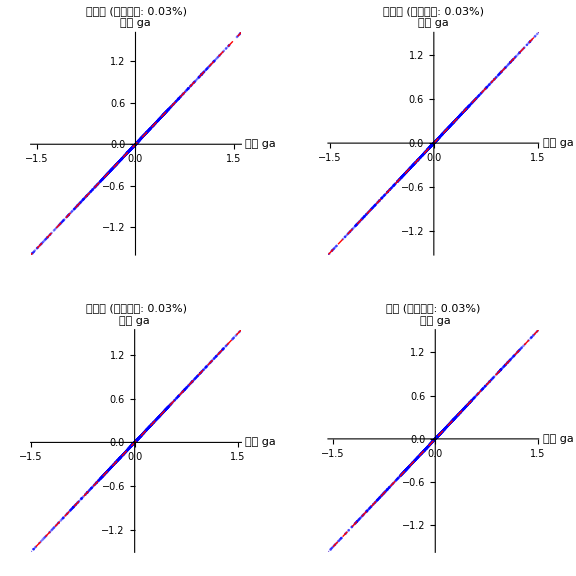

绘制误差分布：

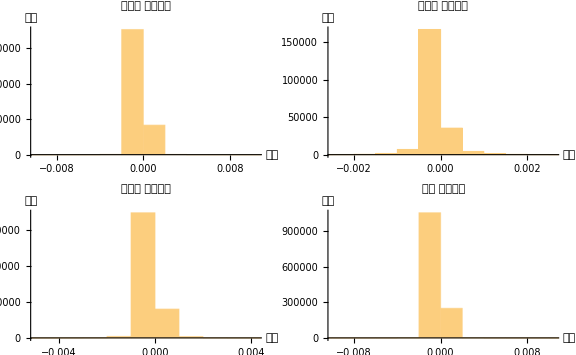

========================================

统计摘要：

========================================

训练集:

样本数: 873655

RMSE: 0.0004

相对误差: 0.03%

最大误差: 0.0501

平均误差: 0.0002

中位误差: 0.0001

验证集:

样本数: 218400

RMSE: 0.0004

相对误差: 0.03%

最大误差: 0.0183

平均误差: 0.0002

中位误差: 0.0001

测试集:

样本数: 218400

RMSE: 0.0004

相对误差: 0.03%

最大误差: 0.0295

平均误差: 0.0002

中位误差: 0.0001

总集:

样本数: 1310455

RMSE: 0.0004

相对误差: 0.03%

最大误差: 0.0501

平均误差: 0.0002

中位误差: 0.0001

✅ 训练完成并保存所有数据到Excel

单独文件:

- training_results.xlsx (训练集，最多10000行)

- validation_results.xlsx (验证集，最多10000行)

- test_results.xlsx (测试集，最多10000行)

- all_results.xlsx (总集，最多10000行)

合并文件:

- combined_results.xlsx (包含4个工作表，每个最多10000行)

```mathematica
(* ==================神经网络训练：参数激励Duffing系统==================*)(*输入:[x,v,κ*cos(Ωt),κ*sin(Ωt)]*)(*输出:[ga]=-c*v-α*x-β*x.b3+κ*x*cos(Ωt)*)ClearAll[MyNormalize,EvaluateOnDataset,ExportToExcel];

(*加载数据*)
trainData=Import["trainData_parametric_duffing.mx"];
valData=Import["valData_parametric_duffing.mx"];
testData=Import["testData_parametric_duffing.mx"];  (*测试集数据*)

Print["数据加载完成："];
Print["  训练集: ",Length[trainData]," 样本"];
Print["  验证集: ",Length[valData]," 样本"];
Print["  测试集: ",Length[testData]," 样本"];
Print["  总计: ",Length[trainData]+Length[valData]+Length[testData]," 样本"];

(*归一化函数*)
MyNormalize[x_,m_,s_]:=(x-m)/s;

(*提取输入/目标*)
allInputs=trainData[[All,1]];
allTargets=trainData[[All,2]];
inDim=Length[allInputs[[1]]];
outDim=Length[allTargets[[1]]];

Print["输入维度: ",inDim,", 输出维度: ",outDim];

(*统计与标准化*)
inputMean=Mean[allInputs];
inputStd=StandardDeviation[allInputs]+10^-10;
targetMean=Mean[allTargets];
targetStd=StandardDeviation[allTargets]+10^-10;

trainDataNorm=Table[MyNormalize[trainData[[i,1]],inputMean,inputStd]->MyNormalize[trainData[[i,2]],targetMean,targetStd],{i,Length[trainData]}];

valDataNorm=Table[MyNormalize[valData[[i,1]],inputMean,inputStd]->MyNormalize[valData[[i,2]],targetMean,targetStd],{i,Length[valData]}];

testDataNorm=Table[MyNormalize[testData[[i,1]],inputMean,inputStd]->MyNormalize[testData[[i,2]],targetMean,targetStd],{i,Length[testData]}];

(*网络架构*)
net=NetChain[{LinearLayer[64],Tanh,LinearLayer[32],Tanh,LinearLayer[outDim]},"Input"->inDim,"Output"->outDim];

(*通用评估函数-可用于任意数据集*)
EvaluateOnDataset[nn_,dataset_,datasetName_String]:=Module[{inputsNorm,predNorm,pred,true,rmseVec,stdTrueVec,relErrVec,score},inputsNorm=Map[MyNormalize[#,inputMean,inputStd]&,dataset[[All,1]]];
predNorm=nn[inputsNorm];
pred=Map[#*targetStd+targetMean&,predNorm];
true=dataset[[All,2]];
rmseVec=Sqrt@Mean[(pred-true)^2];
stdTrueVec=StandardDeviation/@Transpose[true];
relErrVec=100*rmseVec/stdTrueVec;
score=Mean[rmseVec];
Print["\n",datasetName,"评估："];
Print["  RMSE = ",NumberForm[rmseVec,{6,4}]];
Print["  Rel% = ",NumberForm[relErrVec,{5,2}]];
Print["  Score = ",NumberForm[score,{6,4}]];
<|"rmse"->rmseVec,"rel%"->relErrVec,"score"->score,"pred"->pred,"true"->true,"datasetName"->datasetName|>];

(*分阶段训练*)
stages={<|"rounds"->200,"lr"->0.0005|>,<|"rounds"->3000,"lr"->0.0001|>,<|"rounds"->200,"lr"->0.00005|>,<|"rounds"->200,"lr"->0.00001|>};

Print["\n开始多阶段训练..."];

bestNet=net;
bestStats=<|"score"->Infinity|>;
currNet=net;

Do[Print["\n========== Stage ",si," : rounds=",stages[[si,"rounds"]],", lr=",stages[[si,"lr"]]," =========="];
tr=NetTrain[currNet,trainDataNorm,All,ValidationSet->valDataNorm,MaxTrainingRounds->stages[[si,"rounds"]],BatchSize->1024,LearningRate->stages[[si,"lr"]],Method->{"ADAM"},TargetDevice->"CPU",TrainingProgressReporting->"Panel"];
currNet=tr["TrainedNet"];
stats=EvaluateOnDataset[currNet,valData,"验证集"];
If[stats["score"]<bestStats["score"],bestNet=currNet;
bestStats=stats;
Export["checkpoint_best_stage"<>ToString[si]<>".wlnet",bestNet,"WLNet"];
Print["✅ 更新最佳模型已保存"];];,{si,Length[stages]}];

trainedNet=bestNet;

(*保存模型与归一化参数*)
normParams=<|"inputMean"->inputMean,"inputStd"->inputStd,"targetMean"->targetMean,"targetStd"->targetStd,"targetMeanGa"->targetMean[[1]],"targetStdGa"->targetStd[[1]]|>;

Export["normParams_final.mx",normParams,"MX"];
Export["trainedNet_final.wlnet",trainedNet,"WLNet"];

Print["\n✅ 模型已保存"];

(*评估所有数据集*)
Print["\n========================================"];
Print["最终评估："];
Print["========================================"];

trainResults=EvaluateOnDataset[trainedNet,trainData,"训练集"];
valResults=EvaluateOnDataset[trainedNet,valData,"验证集"];
testResults=EvaluateOnDataset[trainedNet,testData,"测试集"];

(*合并所有数据集评估总体性能*)
allData=Join[trainData,valData,testData];
allResults=EvaluateOnDataset[trainedNet,allData,"总集(全部数据)"];

(*Excel导出函数-带采样选项*)
ExportToExcel[yTrue_,yPred_,errors_,filename_,sheetName_,maxRows_:10000]:=Module[{headers,dataRows,outputData,sampleIndices,actualTrue,actualPred,actualErrors},(*如果数据量超过限制，随机采样*)If[Length[yTrue]>maxRows,Print["⚠ ",sheetName,"数据量(",Length[yTrue],")超过限制，随机采样",maxRows,"行"];
sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
(*创建表头*)headers={"真实 ga","预测 ga","误差","绝对误差","相对误差(%)"};
(*创建数据行*)dataRows=Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}];
(*组合表头和数据*)outputData=Join[{headers},dataRows];
(*导出到Excel*)Export[filename,outputData,"XLSX"];
Print["✅ ",sheetName,"数据已导出到: ",filename];
Print["   实际导出行数: ",Length[dataRows]," (不含表头)"];];

(*导出所有数据集-设置每个文件最大行数*)
Print["\n========================================"];
Print["导出Excel文件（限制每个数据集最多10000行）："];
Print["========================================"];

maxRowsPerSheet=10000;  (*可以调整这个数字*)

(*训练集*)
trainTrue=trainResults["true"][[All,1]];
trainPred=trainResults["pred"][[All,1]];
trainErrors=trainPred-trainTrue;
ExportToExcel[trainTrue,trainPred,trainErrors,"training_results.xlsx","训练集",maxRowsPerSheet];

(*验证集*)
valTrue=valResults["true"][[All,1]];
valPred=valResults["pred"][[All,1]];
valErrors=valPred-valTrue;
ExportToExcel[valTrue,valPred,valErrors,"validation_results.xlsx","验证集",maxRowsPerSheet];

(*测试集*)
testTrue=testResults["true"][[All,1]];
testPred=testResults["pred"][[All,1]];
testErrors=testPred-testTrue;
ExportToExcel[testTrue,testPred,testErrors,"test_results.xlsx","测试集",maxRowsPerSheet];

(*总集-所有数据*)
allTrue=allResults["true"][[All,1]];
allPred=allResults["pred"][[All,1]];
allErrors=allPred-allTrue;
ExportToExcel[allTrue,allPred,allErrors,"all_results.xlsx","总集",maxRowsPerSheet];

(*合并Excel文件-每个sheet限制行数*)
CreateSampledData[yTrue_,yPred_,errors_,maxRows_]:=Module[{sampleIndices,actualTrue,actualPred,actualErrors},If[Length[yTrue]>maxRows,sampleIndices=RandomSample[Range[Length[yTrue]],maxRows];
actualTrue=yTrue[[sampleIndices]];
actualPred=yPred[[sampleIndices]];
actualErrors=errors[[sampleIndices]],actualTrue=yTrue;
actualPred=yPred;
actualErrors=errors];
Join[{{"真实 ga","预测 ga","误差","绝对误差","相对误差(%)"}},Table[{actualTrue[[i]],actualPred[[i]],actualErrors[[i]],Abs[actualErrors[[i]]],If[Abs[actualTrue[[i]]]>10^-10,100*Abs[actualErrors[[i]]]/Abs[actualTrue[[i]]],0]},{i,Length[actualTrue]}]]];

Export["combined_results.xlsx",{"训练集"->CreateSampledData[trainTrue,trainPred,trainErrors,maxRowsPerSheet],"验证集"->CreateSampledData[valTrue,valPred,valErrors,maxRowsPerSheet],"测试集"->CreateSampledData[testTrue,testPred,testErrors,maxRowsPerSheet],"总集"->CreateSampledData[allTrue,allPred,allErrors,maxRowsPerSheet]},"XLSX"];

Print["✅ 合并Excel文件已导出: combined_results.xlsx"];
Print["   包含4个工作表: 训练集、验证集、测试集、总集"];
Print["   每个工作表最多",maxRowsPerSheet,"行数据"];

(*可视化：四个数据集的回归图*)
CreateRegressionPlot[yTrue_,yPred_,title_,relErr_]:=Module[{ymin,ymax,sampleIndices,ySample,pSample},(*如果数据太多，抽样显示*)If[Length[yTrue]>2000,sampleIndices=RandomSample[Range[Length[yTrue]],2000];
ySample=yTrue[[sampleIndices]];
pSample=yPred[[sampleIndices]],ySample=yTrue;
pSample=yPred];
ymin=Min[yTrue];
ymax=Max[yTrue];
ListPlot[Transpose[{ySample,pSample}],PlotStyle->{Blue,PointSize[0.005],Opacity[0.5]},PlotLabel->Row[{title," (相对误差: ",NumberForm[relErr,{5,2}],"%)"}],AxesLabel->{"真实 ga","预测 ga"},AspectRatio->1,ImageSize->Medium,Epilog->{Red,Dashed,Line[{{ymin,ymin},{ymax,ymax}}]}]];

Print["\n绘制回归图："];
trainPlot=CreateRegressionPlot[trainTrue,trainPred,"训练集",trainResults["rel%"][[1]]];
valPlot=CreateRegressionPlot[valTrue,valPred,"验证集",valResults["rel%"][[1]]];
testPlot=CreateRegressionPlot[testTrue,testPred,"测试集",testResults["rel%"][[1]]];
allPlot=CreateRegressionPlot[allTrue,allPred,"总集",allResults["rel%"][[1]]];

GraphicsGrid[{{trainPlot,valPlot},{testPlot,allPlot}},ImageSize->Large]

(*误差分布对比*)
CreateErrorHist[errors_,title_]:=Histogram[errors,50,PlotLabel->title<>" 误差分布",AxesLabel->{"误差","频数"},ImageSize->Medium];

Print["\n绘制误差分布："];
trainErrorHist=CreateErrorHist[trainErrors,"训练集"];
valErrorHist=CreateErrorHist[valErrors,"验证集"];
testErrorHist=CreateErrorHist[testErrors,"测试集"];
allErrorHist=CreateErrorHist[allErrors,"总集"];

GraphicsGrid[{{trainErrorHist,valErrorHist},{testErrorHist,allErrorHist}},ImageSize->Large]

(*统计摘要*)
Print["\n========================================"];
Print["统计摘要："];
Print["========================================"];

PrintStats[results_,name_]:=Module[{errors,maxErr,meanErr,medianErr},errors=Abs[results["pred"][[All,1]]-results["true"][[All,1]]];
maxErr=Max[errors];
meanErr=Mean[errors];
medianErr=Median[errors];
Print[name,":"];
Print["  样本数: ",Length[errors]];
Print["  RMSE: ",NumberForm[results["rmse"][[1]],{6,4}]];
Print["  相对误差: ",NumberForm[results["rel%"][[1]],{5,2}],"%"];
Print["  最大误差: ",NumberForm[maxErr,{6,4}]];
Print["  平均误差: ",NumberForm[meanErr,{6,4}]];
Print["  中位误差: ",NumberForm[medianErr,{6,4}]];];

PrintStats[trainResults,"训练集"];
PrintStats[valResults,"验证集"];
PrintStats[testResults,"测试集"];
PrintStats[allResults,"总集"];

Print["\n✅ 训练完成并保存所有数据到Excel"];
Print["   单独文件:"];
Print["   - training_results.xlsx (训练集，最多",maxRowsPerSheet,"行)"];
Print["   - validation_results.xlsx (验证集，最多",maxRowsPerSheet,"行)"];
Print["   - test_results.xlsx (测试集，最多",maxRowsPerSheet,"行)"];
Print["   - all_results.xlsx (总集，最多",maxRowsPerSheet,"行)"];
Print["   合并文件:"];
Print["   - combined_results.xlsx (包含4个工作表，每个最多",maxRowsPerSheet,"行)"];
```

✅ 模型加载完成

━━━━━━━━━━━━━━━━━━━━━━━━━━━

仿真配置：

参数激励: κ=0.1, f_param=1/(2 π) Hz

外激励: F=0.4, f_force=1/(2 π) Hz

初值: x₀=1, v₀=0.

时长: 300 s

━━━━━━━━━━━━━━━━━━━━━━━━━━━

━━ RMSE ━━

x(t): 0.8573

v(t): 0.4325

━━ 庞加莱截面 ━━

周期: T=2 π s (f=1/(2 π) Hz)

截面点数: 32

📊 正在导出数据到 Excel...

抽样: 60001 → 4616 点

✅ 数据已导出: case1_parametric_only.xlsx

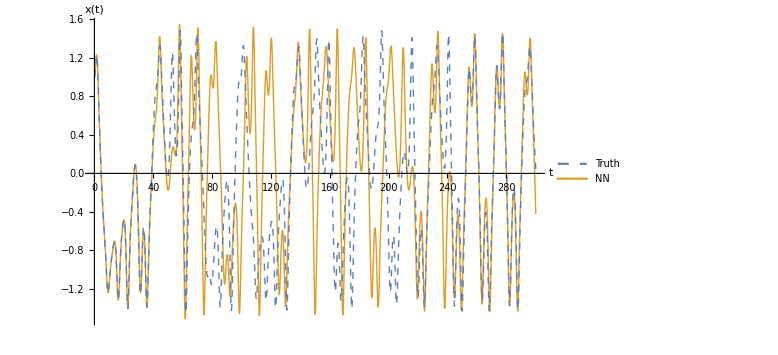

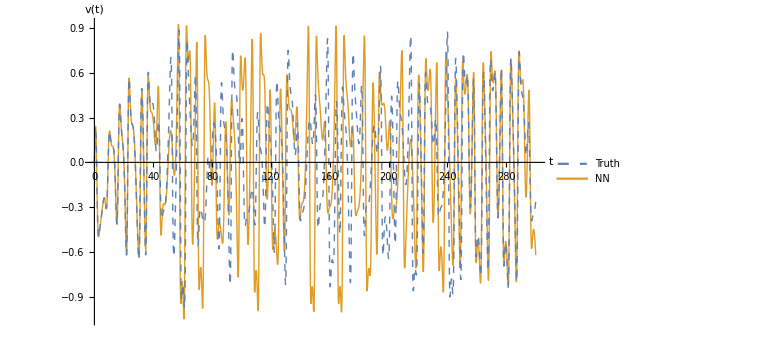

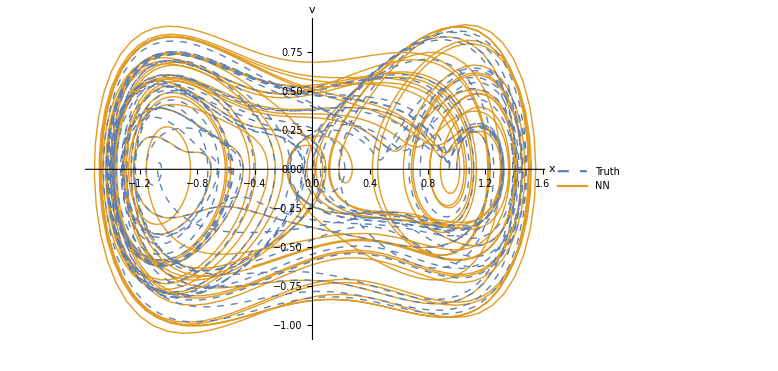

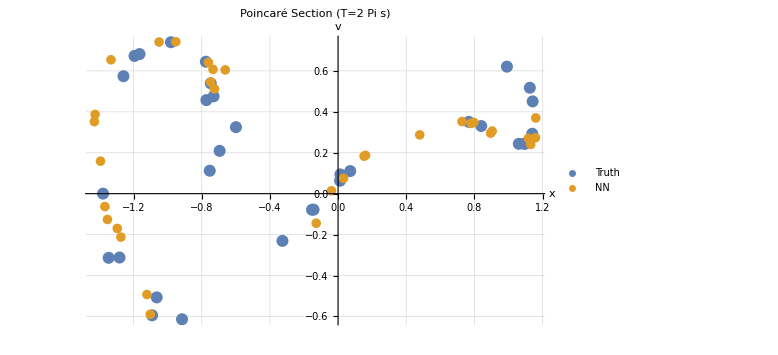

```mathematica
(* =======================1) 载入模型与归一化参数=======================*)
If[!ValueQ[trainedNet],trainedNet=Import["trainedNet_final.wlnet"]];
If[!ValueQ[normParams],normParams=Import["normParams_final.mx"]];

inputMean=Lookup[normParams,"inputMean"];
inputStd=Lookup[normParams,"inputStd"];
targetMean=Lookup[normParams,"targetMean",Lookup[normParams,"targetMeanGa",0.]];
targetStd=Lookup[normParams,"targetStd",Lookup[normParams,"targetStdGa",1.]];
scalar[x_]:=First@Flatten@{x};

Print["✅ 模型加载完成"];

(* =======================2) NN 内部加速度（包含参数激励项）=======================*)
ClearAll[nnInternalAccel];
(*输入:x,v,κ,Ω,t->输出:ga=-c*v-α*x-β*x.b3+κ*x*cos(Ω*t)*)
nnInternalAccel[x_?NumericQ,v_?NumericQ,κ_?NumericQ,Ω_?NumericQ,t_?NumericQ]:=Module[{kc,ks,z,out},kc=κ*Cos[Ω*t];
ks=κ*Sin[Ω*t];
z=({x,v,kc,ks}-inputMean)/inputStd;
out=trainedNet[z];
scalar[out]*scalar[targetStd]+scalar[targetMean]];

(* =======================3) "真值"方程=======================*)
α=-1.;β=1.;c=0.3;
truthAccel[x_,v_,κ_,Ω_,t_]:=-c*v-α*x-β*x^3+κ*x*Cos[Ω*t];

(* =======================4) 求解器：NN 系统& 真值系统=======================*)
ClearAll[SolveNN,SolveTruth];

(*NN求解器：可选外激励*)
SolveNN[freqParam_?NumericQ,κ_?NumericQ,x0_?NumericQ,tEnd_?NumericQ,v0_:0.,freqForce_:0.,forceAmp_:0.]:=Module[{ΩParam=2*Pi*freqParam,ΩForce=2*Pi*freqForce},Check[First@NDSolve[{x''[t]==nnInternalAccel[x[t],x'[t],κ,ΩParam,t]+forceAmp*Cos[ΩForce*t],x[0]==x0,x'[0]==v0},{x,x'},{t,0,tEnd}],$Failed]];

(*真值求解器：可选外激励*)
SolveTruth[freqParam_?NumericQ,κ_?NumericQ,x0_?NumericQ,tEnd_?NumericQ,v0_:0.,freqForce_:0.,forceAmp_:0.]:=Module[{ΩParam=2*Pi*freqParam,ΩForce=2*Pi*freqForce},Check[First@NDSolve[{x''[t]==truthAccel[x[t],x'[t],κ,ΩParam,t]+forceAmp*Cos[ΩForce*t],x[0]==x0,x'[0]==v0},{x,x'},{t,0,tEnd}],$Failed]];

(* =======================5) 对比函数=======================*)
ClearAll[CompareNNvsTruth];
Options[CompareNNvsTruth]={"Dt"->Automatic,"Labels"->{"Truth","NN"},"ExportExcel"->True,"ExcelFilename"->"comparison_parametric.xlsx","ExcelMaxPoints"->5000,"PoincareTransient"->100,"PoincareFreq"->Automatic  (*用于庞加莱截面的频率*)};

CompareNNvsTruth[freqParam_?NumericQ,κ_?NumericQ,x0_?NumericQ,tEnd_?NumericQ,v0_:0.,freqForce_:0.,forceAmp_:0.,OptionsPattern[]]:=Module[{ΩParam=2*Pi*freqParam,ΩForce=2*Pi*freqForce,dt,lbls,solT,solN,xT,vT,xN,vN,tgrid,xTvals,xNvals,vTvals,vNvals,rmseX,rmseV,colorTruth,colorNN,styTruth,styNN,legend,xLine,vLine,phaseLine,exportExcel,excelFile,maxPts,exportStep,tgridExport,dataTable,summaryTable,poincareTransient,period,poincFreq,tPoincare,xTpoincare,vTpoincare,xNpoincare,vNpoincare,poincarePlot},(*样式设置*)colorTruth=RGBColor[0.368,0.507,0.710];
colorNN=RGBColor[0.880,0.611,0.142];
styTruth=Directive[colorTruth,Dashed,Thick];
styNN=Directive[colorNN,Thick];
lbls=OptionValue["Labels"];
legend=Placed[LineLegend[{styTruth,styNN},lbls],After];
exportExcel=OptionValue["ExportExcel"];
excelFile=OptionValue["ExcelFilename"];
maxPts=OptionValue["ExcelMaxPoints"];
poincareTransient=OptionValue["PoincareTransient"];
dt=OptionValue["Dt"]/. Automatic->(1./(200.*Max[1.,freqParam,freqForce]));
(*确定庞加莱截面采样频率*)poincFreq=OptionValue["PoincareFreq"]/. Automatic->If[freqForce>0,freqForce,freqParam];
period=1/poincFreq;
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
Print["仿真配置："];
Print["  参数激励: κ=",κ,", f_param=",NumberForm[freqParam,{4,3}]," Hz"];
If[forceAmp>0,Print["  外激励: F=",forceAmp,", f_force=",NumberForm[freqForce,{4,3}]," Hz"];,Print["  外激励: 无"];];
Print["  初值: x₀=",x0,", v₀=",v0];
Print["  时长: ",tEnd," s"];
Print["━━━━━━━━━━━━━━━━━━━━━━━━━━━"];
(*求解系统*)solT=SolveTruth[freqParam,κ,x0,tEnd,v0,freqForce,forceAmp];
If[solT===$Failed,Print["❌ 真值系统 NDSolve 未收敛。"];
Return[$Failed]];
solN=SolveNN[freqParam,κ,x0,tEnd,v0,freqForce,forceAmp];
If[solN===$Failed,Print["❌ 神经网络系统 NDSolve 未收敛。"];
Return[$Failed]];
xT=x/. solT;vT=x'/. solT;
xN=x/. solN;vN=x'/. solN;
(*生成时间网格和数据*)tgrid=N@Range[0,tEnd,dt];
xTvals=xT/@tgrid;xNvals=xN/@tgrid;
vTvals=vT/@tgrid;vNvals=vN/@tgrid;
(*计算误差指标*)rmseX=Sqrt@Mean[(xNvals-xTvals)^2];
rmseV=Sqrt@Mean[(vNvals-vTvals)^2];
Print["━━ RMSE ━━"];
Print["  x(t): ",NumberForm[rmseX,{6,4}]];
Print["  v(t): ",NumberForm[rmseV,{6,4}]];
(*计算庞加莱截面*)tPoincare=Select[Range[poincareTransient,tEnd,period],#<=tEnd&];
If[Length[tPoincare]>0,xTpoincare=xT/@tPoincare;
vTpoincare=vT/@tPoincare;
xNpoincare=xN/@tPoincare;
vNpoincare=vN/@tPoincare;
Print["━━ 庞加莱截面 ━━"];
Print["  周期: T=",NumberForm[period,{6,4}]," s (f=",NumberForm[poincFreq,{6,4}]," Hz)"];
Print["  截面点数: ",Length[tPoincare]];,Print["⚠️ 警告: 模拟时间太短，无法生成庞加莱截面"];
xTpoincare={};vTpoincare={};
xNpoincare={};vNpoincare={};];
(*Excel导出*)If[exportExcel,Print["📊 正在导出数据到 Excel..."];
If[Length[tgrid]>maxPts,exportStep=Ceiling[Length[tgrid]/maxPts];
tgridExport=tgrid[[1;;-1;;exportStep]];
Print["   抽样: ",Length[tgrid]," → ",Length[tgridExport]," 点"];,tgridExport=tgrid;
exportStep=1;];
dataTable=Join[{{"Time (t)","x_Truth","x_NN","v_Truth","v_NN","Error_x","Error_v"}},Transpose[{tgridExport,(xT/@tgridExport),(xN/@tgridExport),(vT/@tgridExport),(vN/@tgridExport),(xN/@tgridExport)-(xT/@tgridExport),(vN/@tgridExport)-(vT/@tgridExport)}]];
If[Length[tPoincare]>0,poincareTable=Join[{{"Time (t)","x_Truth","v_Truth","x_NN","v_NN"}},Transpose[{tPoincare,xTpoincare,vTpoincare,xNpoincare,vNpoincare}]];,poincareTable={{"Time (t)","x_Truth","v_Truth","x_NN","v_NN"},{"N/A","N/A","N/A","N/A","N/A"}};];
summaryTable={{"Parameter","Value"},{"Parametric Excitation",""},{"  Amplitude (κ)",κ},{"  Frequency (Hz)",freqParam},{"  Omega (rad/s)",ΩParam},{"External Force",""},{"  Amplitude (F)",forceAmp},{"  Frequency (Hz)",freqForce},{"  Omega (rad/s)",ΩForce},{"Initial Conditions",""},{"  Position (x₀)",x0},{"  Velocity (v₀)",v0},{"Simulation",""},{"  Total Time (s)",tEnd},{"  Time Step (dt)",dt},{"  Total Points",Length[tgrid]},{"  Exported Points",Length[tgridExport]},{"Poincare Section",""},{"  Sampling Frequency (Hz)",poincFreq},{"  Period (s)",period},{"  Transient Time (s)",poincareTransient},{"  Points",Length[tPoincare]},{"RMSE Metrics",""},{"  RMSE x(t)",rmseX},{"  RMSE v(t)",rmseV},{"System Parameters",""},{"  Alpha (α)",α},{"  Beta (β)",β},{"  Damping (c)",c}};
Export[excelFile,{"Time History"->dataTable,"Poincare Section"->poincareTable,"Summary"->summaryTable},"XLSX"];
Print["✅ 数据已导出: ",excelFile];];
(*生成图形*)xLine=Plot[{xN[t],xT[t]},{t,0,tEnd},PlotStyle->{styNN,styTruth},PlotLegends->legend,AxesLabel->{"t","x(t)"},PlotRange->All,ImageSize->Large];
vLine=Plot[{vN[t],vT[t]},{t,0,tEnd},PlotStyle->{styNN,styTruth},PlotLegends->legend,AxesLabel->{"t","v(t)"},PlotRange->All,ImageSize->Large];
phaseLine=ParametricPlot[{{xN[t],vN[t]},{xT[t],vT[t]}},{t,0,tEnd},PlotStyle->{styNN,styTruth},PlotLegends->legend,AxesLabel->{"x","v"},PlotRange->All,ImageSize->Large];
If[Length[tPoincare]>0,poincarePlot=ListPlot[{Transpose[{xTpoincare,vTpoincare}],Transpose[{xNpoincare,vNpoincare}]},PlotStyle->{Directive[colorTruth,PointSize[0.015]],Directive[colorNN,PointSize[0.012]]},PlotLegends->Placed[PointLegend[{colorTruth,colorNN},lbls],After],AxesLabel->{"x","v"},PlotLabel->"Poincaré Section (T="<>ToString[NumberForm[period,3]]<>" s)",PlotRange->All,ImageSize->Large,GridLines->Automatic];,poincarePlot=Graphics[Text[Style["庞加莱截面：模拟时间不足",16,Red],{0,0}],ImageSize->Large];];
Print@xLine;
Print@vLine;
Print@phaseLine;
Print@poincarePlot;
<|"TimeGrid"->tgrid,"xTruth"->xTvals,"xNN"->xNvals,"vTruth"->vTvals,"vNN"->vNvals,"PoincareTimes"->tPoincare,"PoincareXTruth"->xTpoincare,"PoincareVTruth"->vTpoincare,"PoincareXNN"->xNpoincare,"PoincareVNN"->vNpoincare,"RMSE_x"->rmseX,"RMSE_v"->rmseV,"Period"->period,"ExcelFile"->If[exportExcel,excelFile,None]|>];

(* =======================6) 使用示例=======================*)




result1=CompareNNvsTruth[1/2/Pi,(*freqParam:参数激励频率*)0.1,(*κ:参数激励幅值*)1,(*x0*)300,(*tEnd*)0.,(*v0*)1/2/Pi,(*freqForce:无外激励*)0.4,(*forceAmp:无外激励*)"ExcelFilename"->"case1_parametric_only.xlsx"];

(*(*案例2:参数激励+外激励*)
Print["\n【案例2】参数激励 + 外激励"];
result2=CompareNNvsTruth[0.15/(2*Pi),(*freqParam*)0.15,(*κ*)1.0,(*x0*)300,(*tEnd*)0.,(*v0*)0.1/(2*Pi),(*freqForce:外激励频率*)0.2,(*forceAmp:外激励幅值*)"ExcelFilename"->"case2_combined.xlsx","PoincareFreq"->0.1/(2*Pi)  (*使用外激励频率做庞加莱截面*)];

(*案例3:主参数共振 (Ω_param≈2*ω_natural)*)
Print["\n【案例3】主参数共振"];
result3=CompareNNvsTruth[2.0/(2*Pi),(*freqParam:接近2倍自然频率*)0.2,(*κ*)0.5,(*x0*)400,(*tEnd*)0.,(*v0*)0.,(*无外激励*)0.,"ExcelFilename"->"case3_principal_resonance.xlsx","PoincareTransient"->200];

Print["\n✅ 所有测试完成！"];*)
```

扫频配置：

参数激励: κ=0.1, f_param=1/(2 π) Hz (固定)

外激励扫频: f_force ∈ [0.0795775, 0.238732] Hz

外激励幅值: F=0.2

前扫进度：

10/201

20/201

30/201

40/201

50/201

60/201

70/201

80/201

90/201

100/201

110/201

120/201

130/201

140/201

150/201

160/201

170/201

180/201

190/201

200/201

201/201

后扫进度：

10/201

20/201

30/201

40/201

50/201

60/201

70/201

80/201

90/201

100/201

110/201

120/201

130/201

140/201

150/201

160/201

170/201

180/201

190/201

200/201

201/201

绘制幅频响应曲线：

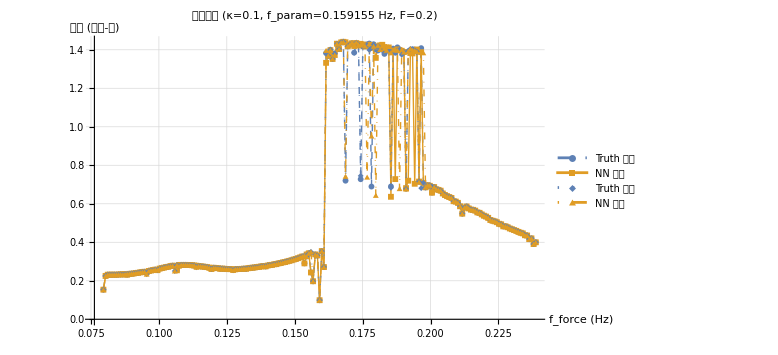

绘制RMSE误差曲线：

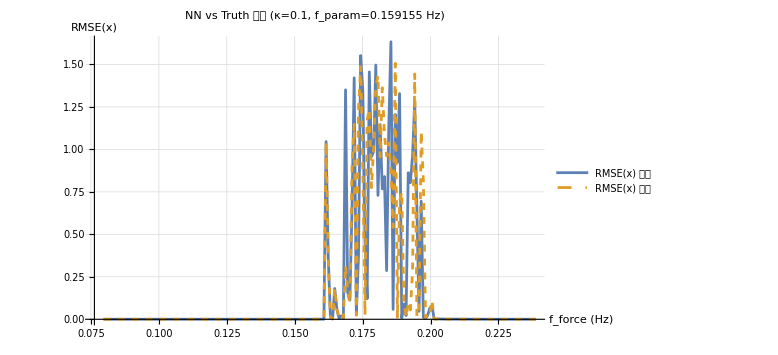

✅ 数据已保存到: frf_parametric_force_sweep.mx

```mathematica
(* ======================NN& 真值：固定参数激励，扫描外激励频率======================*)ClearAll[FRFSweepForceWithParam,PlotFRFNNTruth,PlotRMSEFRF];

FRFSweepForceWithParam[freqParamFixed_?NumericQ,(*固定的参数激励频率*)kappaFixed_?NumericQ,(*固定的参数激励幅值*)freqForceMin_:0.5,(*外激励频率范围*)freqForceMax_:1.5,dFreqForce_:0.01,forceAmp_:0.2,(*外激励幅值*)cyclesSettle_:60,cyclesMeasure_:20,dt_:Automatic,ic_:Automatic,carryFrom_:"truth"]:=Module[{stables,ic0,doOne,updateIC,forwardGrid,backwardGrid,forward={},backward={},initTruth,initNN,ΩParam},ΩParam=2*Pi*freqParamFixed;
(*起始平衡（右井）*)stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["❌ 未找到两个稳定平衡"];
Return[$Failed]];
ic0=If[ic===Automatic,{stables[[2]],0.0},ic];
Print["扫频配置："];
Print["  参数激励: κ=",kappaFixed,", f_param=",NumberForm[freqParamFixed,{4,3}]," Hz (固定)"];
Print["  外激励扫频: f_force ∈ [",freqForceMin,", ",freqForceMax,"] Hz"];
Print["  外激励幅值: F=",forceAmp];
(*单个频点：两套系统同步积分与度量*)doOne[freqForce_?NumericQ,{x0T_,v0T_},{x0N_,v0N_}]:=Module[{T,tS,tM,tEnd,dtsamp,solT,solN,xT,vT,xN,vN,ts,xTs,vTs,xNs,vNs,xminT,xmaxT,xminN,xmaxN,ampT,ampN,meanT,meanN,rmx,rmv,lastT,lastN,okT=True,okN=True},T=1/freqForce;(*基于外激励周期*)tS=cyclesSettle*T;
tM=cyclesMeasure*T;
tEnd=tS+tM;
dtsamp=Replace[dt,Automatic->(1./(200.*Max[freqForce,freqParamFixed]))];
(*真值求解*)solT=SolveTruth[freqParamFixed,kappaFixed,x0T,tEnd,v0T,freqForce,forceAmp];
If[solT===$Failed,okT=False,xT=x/. solT;
vT=x'/. solT];
(*NN求解*)solN=SolveNN[freqParamFixed,kappaFixed,x0N,tEnd,v0N,freqForce,forceAmp];
If[solN===$Failed,okN=False,xN=x/. solN;
vN=x'/. solN];
(*采样与度量*)ts=Range[tS,tEnd,dtsamp];
If[okT,xTs=xT/@ts;vTs=vT/@ts;
xminT=Min[xTs];xmaxT=Max[xTs];meanT=Mean[xTs];
ampT=(xmaxT-xminT)/2.;
lastT={xT[tEnd],vT[tEnd]},lastT={x0T,v0T}];
If[okN,xNs=xN/@ts;vNs=vN/@ts;
xminN=Min[xNs];xmaxN=Max[xNs];meanN=Mean[xNs];
ampN=(xmaxN-xminN)/2.;
lastN={xN[tEnd],vN[tEnd]},lastN={x0N,v0N}];
If[okT&&okN,rmx=Sqrt@Mean[(xNs-xTs)^2];
rmv=Sqrt@Mean[(vNs-vTs)^2],rmx=Missing[];
rmv=Missing[]];
<|"freqForce"->freqForce,"Truth"-><|"Amp"->ampT,"Mean"->meanT,"xmax"->xmaxT,"xmin"->xminT,"ok"->okT|>,"NN"-><|"Amp"->ampN,"Mean"->meanN,"xmax"->xmaxN,"xmin"->xminN,"ok"->okN|>,"RMSE"-><|"x"->rmx,"v"->rmv|>,"endTruth"->lastT,"endNN"->lastN|>];
(*续接策略*)updateIC[res_Association]:=Module[{xvT=res["endTruth"],xvN=res["endNN"]},Switch[carryFrom,"truth",{xvT,xvT},"nn",{xvN,xvN},"self"|"independent",{xvT,xvN},_,{xvT,xvT}]];
(*前扫*)forwardGrid=Range[freqForceMin,freqForceMax,dFreqForce];
{initTruth,initNN}={ic0,ic0};
Print["前扫进度："];
Do[If[Mod[i,10]==0||i==Length[forwardGrid],Print["  ",i,"/",Length[forwardGrid]]];
With[{r=doOne[forwardGrid[[i]],initTruth,initNN]},AppendTo[forward,KeyDrop[r,{"endTruth","endNN"}]];
{initTruth,initNN}=updateIC[r]],{i,Length[forwardGrid]}];
(*后扫：先在 freqForceMax 热身*){initTruth,initNN}=updateIC[doOne[freqForceMax,ic0,ic0]];
backwardGrid=Range[freqForceMax,freqForceMin,-dFreqForce];
Print["后扫进度："];
Do[If[Mod[i,10]==0||i==Length[backwardGrid],Print["  ",i,"/",Length[backwardGrid]]];
With[{r=doOne[backwardGrid[[i]],initTruth,initNN]},AppendTo[backward,KeyDrop[r,{"endTruth","endNN"}]];
{initTruth,initNN}=updateIC[r]],{i,Length[backwardGrid]}];
<|"forward"->forward,"backward"->backward,"meta"-><|"freqParam"->freqParamFixed,"kappa"->kappaFixed,"forceAmp"->forceAmp,"cyclesSettle"->cyclesSettle,"cyclesMeasure"->cyclesMeasure,"dt"->dt,"carryFrom"->carryFrom|>|>];

(* ============================绘图：幅频比较============================*)
PlotFRFNNTruth[frf_Association,key_:"Amp"]:=Module[{extract,fT,fN,bT,bN,meta},extract[dir_,model_]:=Module[{lst=frf[dir]},Cases[lst,a_Association/;KeyExistsQ[a,model]&&NumericQ[a[model][key]]:>{a["freqForce"],a[model][key]}]];
fT=extract["forward","Truth"];
fN=extract["forward","NN"];
bT=extract["backward","Truth"];
bN=extract["backward","NN"];
meta=frf["meta"];
ListLinePlot[{fT,fN,bT,bN},PlotLegends->{"Truth 前扫","NN 前扫","Truth 后扫","NN 后扫"},PlotStyle->{Directive[RGBColor[0.368,0.507,0.710],Dashed,Thick],Directive[RGBColor[0.880,0.611,0.142],Thick],Directive[RGBColor[0.368,0.507,0.710],Dotted,Thick],Directive[RGBColor[0.880,0.611,0.142],DotDashed,Thick]},PlotMarkers->{Automatic,6},AxesLabel->{"f_force (Hz)",Switch[key,"Amp","幅值 (半峰-峰)","Mean","均值",_,key]},PlotLabel->StringTemplate["频率响应 (κ=``, f_param=`` Hz, F=``)"][meta["kappa"],meta["freqParam"],meta["forceAmp"]],GridLines->Automatic,ImageSize->Large,PlotRange->All]];

(* ============================绘图：RMSE 随频率============================*)
PlotRMSEFRF[frf_Association,comp_:"x"]:=Module[{ext,meta},ext[dir_]:=Module[{lst=frf[dir]},Cases[lst,a_Association/;!MissingQ[a["RMSE"][comp]]&&NumericQ[a["RMSE"][comp]]:>{a["freqForce"],a["RMSE"][comp]}]];
meta=frf["meta"];
ListLinePlot[{ext["forward"],ext["backward"]},PlotLegends->{"RMSE("<>comp<>") 前扫","RMSE("<>comp<>") 后扫"},PlotStyle->{Directive[Thick],Directive[Dashed,Thick]},AxesLabel->{"f_force (Hz)","RMSE("<>comp<>")"},PlotLabel->StringTemplate["NN vs Truth 误差 (κ=``, f_param=`` Hz)"][meta["kappa"],meta["freqParam"]],GridLines->Automatic,ImageSize->Large,PlotRange->All]];

(* ============================使用示例============================*)


(*测试1:固定参数激励，扫描外激励频率*)

frf1=FRFSweepForceWithParam[1/(2*Pi),(*参数激励频率 (固定)*)0.1,(*参数激励幅值 (固定)*)0.5/(2*Pi),(*外激励频率最小值*)1.5/(2*Pi),(*外激励频率最大值*)0.005/(2*Pi),(*频率步长*)0.2,(*外激励幅值*)60,(*稳定周期数*)20,(*测量周期数*)Automatic,(*时间步长*)Automatic,(*初始条件*)"truth"          (*续接策略*)];

Print["\n绘制幅频响应曲线："];
PlotFRFNNTruth[frf1,"Amp"]

Print["\n绘制RMSE误差曲线："];
PlotRMSEFRF[frf1,"x"]


(* ============================导出数据============================*)
Export["frf_parametric_force_sweep.mx",frf1,"MX"];
Print["✅ 数据已保存到: frf_parametric_force_sweep.mx"];

(* ============================导出到Excel============================*)

(*提取前扫数据*)
forwardData=Module[{lst=frf1["forward"]},Table[With[{a=lst[[i]]},{a["freqForce"],a["Truth"]["Amp"],a["Truth"]["Mean"],a["Truth"]["xmax"],a["Truth"]["xmin"],a["NN"]["Amp"],a["NN"]["Mean"],a["NN"]["xmax"],a["NN"]["xmin"],If[MissingQ[a["RMSE"]["x"]],"",a["RMSE"]["x"]],If[MissingQ[a["RMSE"]["v"]],"",a["RMSE"]["v"]]}],{i,Length[lst]}]];

(*提取后扫数据*)
backwardData=Module[{lst=frf1["backward"]},Table[With[{a=lst[[i]]},{a["freqForce"],a["Truth"]["Amp"],a["Truth"]["Mean"],a["Truth"]["xmax"],a["Truth"]["xmin"],a["NN"]["Amp"],a["NN"]["Mean"],a["NN"]["xmax"],a["NN"]["xmin"],If[MissingQ[a["RMSE"]["x"]],"",a["RMSE"]["x"]],If[MissingQ[a["RMSE"]["v"]],"",a["RMSE"]["v"]]}],{i,Length[lst]}]];

(*创建表头*)
headers={"f_force (Hz)","Truth_Amp","Truth_Mean","Truth_xmax","Truth_xmin","NN_Amp","NN_Mean","NN_xmax","NN_xmin","RMSE_x","RMSE_v"};

(*添加元数据*)
meta=frf1["meta"];
metaInfo={{"参数激励频率 (Hz)",meta["freqParam"]},{"参数激励幅值",meta["kappa"]},{"外激励幅值",meta["forceAmp"]},{"稳定周期数",meta["cyclesSettle"]},{"测量周期数",meta["cyclesMeasure"]},{"续接策略",meta["carryFrom"]},{"",""}};

(*组合前扫数据*)
forwardSheet=Join[{{"前扫数据 (Forward Sweep)"}},metaInfo,{headers},forwardData];

(*组合后扫数据*)
backwardSheet=Join[{{"后扫数据 (Backward Sweep)"}},metaInfo,{headers},backwardData];

(*导出到Excel*)
Export["FRF_Results.xlsx",{"Forward"->forwardSheet,"Backward"->backwardSheet},"XLSX"];
```

```mathematica
(* ======================NN& 真值：固定外激励，扫描参数激励频率======================*)ClearAll[FRFSweepParamWithForce,PlotFRFNNTruth,PlotRMSEFRF];

FRFSweepParamWithForce[freqForceFixed_?NumericQ,(*固定的外激励频率*)forceAmpFixed_?NumericQ,(*固定的外激励幅值*)freqParamMin_:0.5,(*参数激励频率范围*)freqParamMax_:1.5,dFreqParam_:0.01,(*参数激励频率步长*)kappa_:0.15,(*参数激励幅值*)cyclesSettle_:60,cyclesMeasure_:20,dt_:Automatic,ic_:Automatic,carryFrom_:"truth"]:=Module[{stables,ic0,doOne,updateIC,forwardGrid,backwardGrid,forward={},backward={},initTruth,initNN,ΩForce},ΩForce=2*Pi*freqForceFixed;
(*起始平衡（右井）*)stables=FindStableEq[α,β,0];
If[Length[stables]<2,Print["❌ 未找到两个稳定平衡"];
Return[$Failed]];
ic0=If[ic===Automatic,{stables[[2]],0.0},ic];
Print["扫频配置："];
Print["  外激励: F=",forceAmpFixed,", f_force=",NumberForm[freqForceFixed,{4,3}]," Hz (固定)"];
Print["  参数激励扫频: f_param ∈ [",freqParamMin,", ",freqParamMax,"] Hz"];
Print["  参数激励幅值: κ=",kappa];
(*单个频点：两套系统同步积分与度量*)doOne[freqParam_?NumericQ,{x0T_,v0T_},{x0N_,v0N_}]:=Module[{T,tS,tM,tEnd,dtsamp,solT,solN,xT,vT,xN,vN,ts,xTs,vTs,xNs,vNs,xminT,xmaxT,xminN,xmaxN,ampT,ampN,meanT,meanN,rmx,rmv,lastT,lastN,okT=True,okN=True},(*基于外激励和参数激励中的最高频率*)T=1/Max[freqForceFixed,freqParam];
tS=cyclesSettle*T;
tM=cyclesMeasure*T;
tEnd=tS+tM;
dtsamp=Replace[dt,Automatic->(1./(200.*Max[freqForceFixed,freqParam]))];
(*真值求解*)solT=SolveTruth[freqParam,kappa,x0T,tEnd,v0T,freqForceFixed,forceAmpFixed];
If[solT===$Failed,okT=False,xT=x/. solT;
vT=x'/. solT];
(*NN求解*)solN=SolveNN[freqParam,kappa,x0N,tEnd,v0N,freqForceFixed,forceAmpFixed];
If[solN===$Failed,okN=False,xN=x/. solN;
vN=x'/. solN];
(*采样与度量*)ts=Range[tS,tEnd,dtsamp];
If[okT,xTs=xT/@ts;vTs=vT/@ts;
xminT=Min[xTs];xmaxT=Max[xTs];meanT=Mean[xTs];
ampT=(xmaxT-xminT)/2.;
lastT={xT[tEnd],vT[tEnd]},lastT={x0T,v0T}];
If[okN,xNs=xN/@ts;vNs=vN/@ts;
xminN=Min[xNs];xmaxN=Max[xNs];meanN=Mean[xNs];
ampN=(xmaxN-xminN)/2.;
lastN={xN[tEnd],vN[tEnd]},lastN={x0N,v0N}];
If[okT&&okN,rmx=Sqrt@Mean[(xNs-xTs)^2];
rmv=Sqrt@Mean[(vNs-vTs)^2],rmx=Missing[];
rmv=Missing[]];
<|"freqParam"->freqParam,"Truth"-><|"Amp"->ampT,"Mean"->meanT,"xmax"->xmaxT,"xmin"->xminT,"ok"->okT|>,"NN"-><|"Amp"->ampN,"Mean"->meanN,"xmax"->xmaxN,"xmin"->xminN,"ok"->okN|>,"RMSE"-><|"x"->rmx,"v"->rmv|>,"endTruth"->lastT,"endNN"->lastN|>];
(*续接策略*)updateIC[res_Association]:=Module[{xvT=res["endTruth"],xvN=res["endNN"]},Switch[carryFrom,"truth",{xvT,xvT},"nn",{xvN,xvN},"self"|"independent",{xvT,xvN},_,{xvT,xvT}]];
(*前扫*)forwardGrid=Range[freqParamMin,freqParamMax,dFreqParam];
{initTruth,initNN}={ic0,ic0};
Print["前扫进度："];
Do[If[Mod[i,10]==0||i==Length[forwardGrid],Print["  ",i,"/",Length[forwardGrid]]];
With[{r=doOne[forwardGrid[[i]],initTruth,initNN]},AppendTo[forward,KeyDrop[r,{"endTruth","endNN"}]];
{initTruth,initNN}=updateIC[r]],{i,Length[forwardGrid]}];
(*后扫：先在 freqParamMax 热身*){initTruth,initNN}=updateIC[doOne[freqParamMax,ic0,ic0]];
backwardGrid=Range[freqParamMax,freqParamMin,-dFreqParam];
Print["后扫进度："];
Do[If[Mod[i,10]==0||i==Length[backwardGrid],Print["  ",i,"/",Length[backwardGrid]]];
With[{r=doOne[backwardGrid[[i]],initTruth,initNN]},AppendTo[backward,KeyDrop[r,{"endTruth","endNN"}]];
{initTruth,initNN}=updateIC[r]],{i,Length[backwardGrid]}];
<|"forward"->forward,"backward"->backward,"meta"-><|"freqForce"->freqForceFixed,"forceAmp"->forceAmpFixed,"kappa"->kappa,"cyclesSettle"->cyclesSettle,"cyclesMeasure"->cyclesMeasure,"dt"->dt,"carryFrom"->carryFrom|>|>];

(* ============================绘图：幅频比较============================*)
PlotFRFNNTruth[frf_Association,key_:"Amp"]:=Module[{extract,fT,fN,bT,bN,meta},extract[dir_,model_]:=Module[{lst=frf[dir]},(*这里改为方括号*)Cases[lst,a_Association/;KeyExistsQ[a,model]&&NumericQ[a[model][key]]:>{a["freqParam"],a[model][key]}]];
fT=extract["forward","Truth"];
fN=extract["forward","NN"];
bT=extract["backward","Truth"];
bN=extract["backward","NN"];
meta=frf["meta"];
ListLinePlot[{fT,fN,bT,bN},PlotLegends->{"Truth 前扫","NN 前扫","Truth 后扫","NN 后扫"},PlotStyle->{Directive[RGBColor[0.368,0.507,0.710],Dashed,Thick],Directive[RGBColor[0.880,0.611,0.142],Thick],Directive[RGBColor[0.368,0.507,0.710],Dotted,Thick],Directive[RGBColor[0.880,0.611,0.142],DotDashed,Thick]},PlotMarkers->{Automatic,6},AxesLabel->{"f_param (Hz)",Switch[key,"Amp","幅值 (半峰-峰)","Mean","均值",_,key]},PlotLabel->StringTemplate["频率响应 (F=``, f_force=`` Hz, κ=``)"][meta["forceAmp"],meta["freqForce"],meta["kappa"]],GridLines->Automatic,ImageSize->Large,PlotRange->All]];

(* ============================绘图：RMSE 随频率============================*)
PlotRMSEFRF[frf_Association,comp_:"x"]:=Module[{ext,meta},ext[dir_]:=Module[{lst=frf[dir]},Cases[lst,a_Association/;!MissingQ[a["RMSE"][comp]]&&NumericQ[a["RMSE"][comp]]:>{a["freqParam"],a["RMSE"][comp]}]];
meta=frf["meta"];
ListLinePlot[{ext["forward"],ext["backward"]},PlotLegends->{"RMSE("<>comp<>") 前扫","RMSE("<>comp<>") 后扫"},PlotStyle->{Directive[Thick],Directive[Dashed,Thick]},AxesLabel->{"f_param (Hz)","RMSE("<>comp<>")"},PlotLabel->StringTemplate["NN vs Truth 误差 (F=``, f_force=`` Hz)"][meta["forceAmp"],meta["freqForce"]],GridLines->Automatic,ImageSize->Large,PlotRange->All]];

(* ============================使用示例============================*)

Print["\n==================== 扫频测试 ====================\n"];

(*测试1:固定外激励，扫描参数激励频率*)
Print["【测试1】固定外激励 (F=0.2, f_force=0.8 Hz)，扫描参数激励"];
frf1=FRFSweepParamWithForce[1/(2*Pi),(*外激励频率 (固定)*)0.1,(*外激励幅值 (固定)*)0.5/(2*Pi),(*参数激励频率最小值*)1.5/(2*Pi),(*参数激励频率最大值*)0.005/(2*Pi),(*频率步长*)0.2,(*参数激励幅值*)60,(*稳定周期数*)20,(*测量周期数*)Automatic,(*时间步长*)Automatic,(*初始条件*)"truth"              (*续接策略*)];

Print["\n绘制幅频响应曲线："];
PlotFRFNNTruth[frf1,"Amp"]

Print["\n绘制RMSE误差曲线："];
PlotRMSEFRF[frf1,"x"]

(* ============================导出数据============================*)
Export["frf_force_param_sweep.mx",frf1,"MX"];
Print["✅ 数据已保存到: frf_force_param_sweep.mx"];

(* ============================导出到Excel============================*)

(*提取前扫数据*)
forwardData=Module[{lst=frf1["forward"]},Table[With[{a=lst[[i]]},{a["freqParam"],a["Truth"]["Amp"],a["Truth"]["Mean"],a["Truth"]["xmax"],a["Truth"]["xmin"],a["NN"]["Amp"],a["NN"]["Mean"],a["NN"]["xmax"],a["NN"]["xmin"],If[MissingQ[a["RMSE"]["x"]],"",a["RMSE"]["x"]],If[MissingQ[a["RMSE"]["v"]],"",a["RMSE"]["v"]]}],{i,Length[lst]}]];

(*提取后扫数据*)
backwardData=Module[{lst=frf1["backward"]},Table[With[{a=lst[[i]]},{a["freqParam"],a["Truth"]["Amp"],a["Truth"]["Mean"],a["Truth"]["xmax"],a["Truth"]["xmin"],a["NN"]["Amp"],a["NN"]["Mean"],a["NN"]["xmax"],a["NN"]["xmin"],If[MissingQ[a["RMSE"]["x"]],"",a["RMSE"]["x"]],If[MissingQ[a["RMSE"]["v"]],"",a["RMSE"]["v"]]}],{i,Length[lst]}]];

(*创建表头*)
headers={"f_param (Hz)","Truth_Amp","Truth_Mean","Truth_xmax","Truth_xmin","NN_Amp","NN_Mean","NN_xmax","NN_xmin","RMSE_x","RMSE_v"};

(*添加元数据*)
meta=frf1["meta"];
metaInfo={{"外激励频率 (Hz)",meta["freqForce"]},{"外激励幅值",meta["forceAmp"]},{"参数激励幅值",meta["kappa"]},{"稳定周期数",meta["cyclesSettle"]},{"测量周期数",meta["cyclesMeasure"]},{"续接策略",meta["carryFrom"]},{"",""}};

(*组合前扫数据*)
forwardSheet=Join[{{"前扫数据 (Forward Sweep)"}},metaInfo,{headers},forwardData];

(*组合后扫数据*)
backwardSheet=Join[{{"后扫数据 (Backward Sweep)"}},metaInfo,{headers},backwardData];

(*导出到Excel*)
Export["FRF_Param_Sweep_Results.xlsx",{"Forward"->forwardSheet,"Backward"->backwardSheet},"XLSX"];

Print["\n✅ Excel数据已导出到: FRF_Param_Sweep_Results.xlsx"];
Print["   - Sheet 1: Forward (前扫数据)"];
Print["   - Sheet 2: Backward (后扫数据)"];
```

==================== 扫频测试 ====================

【测试1】固定外激励 (F=0.2, f_force=0.8 Hz)，扫描参数激励

扫频配置：

外激励: F=0.1, f_force=1/(2 π) Hz (固定)

参数激励扫频: f_param ∈ [0.0795775, 0.238732] Hz

参数激励幅值: κ=0.2

前扫进度：

$Aborted

绘制幅频响应曲线：

-Graphics-

绘制RMSE误差曲线：

-Graphics-

✅ 数据已保存到: frf_force_param_sweep.mx

✅ Excel数据已导出到: FRF_Param_Sweep_Results.xlsx

- Sheet 1: Forward (前扫数据)

- Sheet 2: Backward (后扫数据)

🔄 正在计算庞加莱截面分岔图（参数激励系统）...

参数激励: κ = 0., f_param = 0.016 Hz (固定)

外激励幅值: F = 0.2 (固定)

外激励频率范围: {0.0795775,0.238732} Hz，共 300 个点

截面相位: φ = 0.00 rad

瞬态周期: 200，稳态周期: 100

📊 计算 NN 系统...

✅ NN 完成！共 30000 个点

📊 计算 Truth 系统...

✅ Truth 完成！共 30000 个点

💾 正在导出数据到 PoincareBifurcation_Param.xlsx...

✅ 数据已成功导出到: PoincareBifurcation_Param.xlsx

- Truth系统: 30000 个数据点

- NN系统: 30000 个数据点

✨ 庞加莱截面分岔图绘制完成！

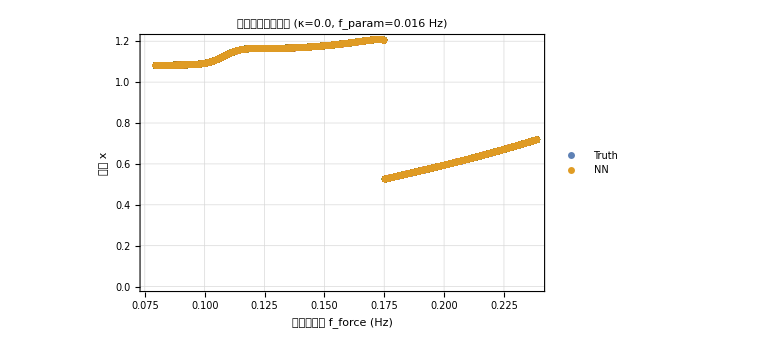

```mathematica
ClearAll[LocalMaxBifurcationForce];

Options[LocalMaxBifurcationForce]={"ParamFreq"->0.1/(2*Pi),(*参数激励频率 (固定,Hz)*)"ParamAmplitude"->0.,(*参数激励幅值 κ (固定)*)"ForceFreqRange"->{0.5/(2*Pi),1.5/(2*Pi)},(*外激励频率范围 (Hz)*)"ForceAmplitude"->0.3,(*外激励幅值 F (固定)*)"FreqPoints"->300,(*频率采样点数*)"TransientCycles"->200,(*瞬态周期数(丢弃)*)"SteadyCycles"->200,(*稳态周期数(采样)*)"InitialCondition"->{1.,0.},(*初始条件 {x0,v0}*)"PlotBoth"->True,(*是否同时绘制 NN 和 Truth*)"PlotVelocity"->False,(*True:绘制速度;False:绘制位移*)"ExportData"->True,(*是否导出数据*)"ExportPath"->"LocalMaxBifurcation_Force.xlsx" (*导出文件路径*)};

LocalMaxBifurcationForce[OptionsPattern[]]:=Module[{freqParam,kappaParam,forceAmp,freqRange,nFreq,nTrans,nSteady,ic,plotBoth,plotV,freqs,results,makeData,plotData,colorTruth,colorNN,yLabel,exportData,exportPath},(*读取参数*)freqParam=OptionValue["ParamFreq"];
kappaParam=OptionValue["ParamAmplitude"];
forceAmp=OptionValue["ForceAmplitude"];
freqRange=OptionValue["ForceFreqRange"];
nFreq=OptionValue["FreqPoints"];
nTrans=OptionValue["TransientCycles"];
nSteady=OptionValue["SteadyCycles"];
ic=OptionValue["InitialCondition"];
plotBoth=OptionValue["PlotBoth"];
plotV=OptionValue["PlotVelocity"];
exportData=OptionValue["ExportData"];
exportPath=OptionValue["ExportPath"];
colorTruth=RGBColor[0.368,0.507,0.710];
colorNN=RGBColor[0.880,0.611,0.142];
(*生成频率点*)freqs=N@Range[freqRange[[1]],freqRange[[2]],(freqRange[[2]]-freqRange[[1]])/(nFreq-1)];
yLabel=If[plotV,"速度局部最大值 v_max","位移局部最大值 x_max"];
(*打印配置信息*)Print["🔄 正在计算局部最大值分岔图(扫描外激励频率)..."];
Print["参数激励: κ = ",kappaParam,", f_param = ",NumberForm[freqParam,{4,3}]," Hz (固定)"];
Print["外激励幅值: F = ",forceAmp," (固定)"];
Print["外激励频率范围: ",freqRange," Hz,共 ",nFreq," 个点"];
Print["瞬态周期: ",nTrans,",稳态周期: ",nSteady];
(*局部最大值提取函数*)makeData[solver_,label_]:=Module[{data={},sol,func,T,tTotal,tStart,localMaxVals,freqForce,timePoints,values,maxIndices},Monitor[Do[(*基于外激励和参数激励中的最高频率来确定周期*)T=1./Max[freqForce,freqParam];
tTotal=(nTrans+nSteady)*T;
tStart=nTrans*T;
(*求解:固定参数激励,变化外激励频率*)sol=solver[freqParam,kappaParam,ic[[1]],tTotal,ic[[2]],freqForce,forceAmp];
If[sol===$Failed,Print["⚠️ ",label," 在外激励频率 ",NumberForm[freqForce,{4,3}]," Hz 处求解失败"];
Continue[]];
(*获取位移或速度函数*)func=If[plotV,x'/. sol,x/. sol];
(*在稳态区间内密集采样*)timePoints=Range[tStart,tTotal,0.01];(*每0.01秒采样一次*)values=func/@timePoints;
(*找到局部最大值的索引*)(*一个点是局部最大值,当且仅当它大于前后相邻的点*)maxIndices=Position[Table[If[i==1||i==Length[values],False,values[[i]]>values[[i-1]]&&values[[i]]>values[[i+1]]],{i,Length[values]}],True]//Flatten;
(*提取局部最大值*)localMaxVals=values[[maxIndices]];
(*存储 (外激励频率,局部最大值) 对*)If[Length[localMaxVals]>0,data=Join[data,Transpose[{ConstantArray[freqForce,Length[localMaxVals]],localMaxVals}]]];,{freqForce,freqs}],Row[{ProgressIndicator[freqForce,freqRange],"  ",NumberForm[freqForce,{4,3}]," Hz"}]];
data];
(*计算 NN 和/或 Truth 数据*)If[plotBoth,Print["\n📊 计算 NN 系统..."];
results=<|"NN"->makeData[SolveNN,"NN"]|>;
Print["✅ NN 完成!共 ",Length[results["NN"]]," 个局部最大值"];
Print["\n📊 计算 Truth 系统..."];
results=Append[results,"Truth"->makeData[SolveTruth,"Truth"]];
Print["✅ Truth 完成!共 ",Length[results["Truth"]]," 个局部最大值"];
(*绘制对比图*)plotData=ListPlot[{results["Truth"],results["NN"]},PlotStyle->{Directive[colorTruth,PointSize[0.008],Opacity[0.7]],Directive[colorNN,PointSize[0.008],Opacity[0.7]]},PlotLegends->Placed[LineLegend[{Directive[colorTruth,PointSize[0.02]],Directive[colorNN,PointSize[0.02]]},{"Truth","NN"}],After],AxesLabel->{Style["外激励频率 f_force (Hz)",14],Style[yLabel,14]},PlotLabel->Style[StringTemplate["局部最大值分岔图 (κ=``, f_param=`` Hz)"][kappaParam,NumberForm[freqParam,{4,3}]],Bold,16],ImageSize->Large,Frame->True,GridLines->Automatic,AspectRatio->0.6];
(*导出数据*)If[exportData,Print["\n💾 正在导出数据到 ",exportPath,"..."];
Export[exportPath,{"Truth系统"->Prepend[results["Truth"],{"外激励频率 (Hz)",yLabel}],"NN系统"->Prepend[results["NN"],{"外激励频率 (Hz)",yLabel}],"参数信息"->{{"参数","值"},{"参数激励频率 (Hz)",freqParam},{"参数激励幅值 κ",kappaParam},{"外激励幅值 F",forceAmp},{"外激励频率范围起点 (Hz)",freqRange[[1]]},{"外激励频率范围终点 (Hz)",freqRange[[2]]},{"频率采样点数",nFreq},{"瞬态周期数",nTrans},{"稳态周期数",nSteady},{"初始位移",ic[[1]]},{"初始速度",ic[[2]]},{"绘制变量",yLabel}}}];
Print["✅ 数据已成功导出到: ",exportPath];
Print["   - Truth系统: ",Length[results["Truth"]]," 个数据点"];
Print["   - NN系统: ",Length[results["NN"]]," 个数据点"];];,(*仅绘制 NN*)Print["\n📊 计算 NN 系统..."];
results=makeData[SolveNN,"NN"];
Print["✅ 完成!共 ",Length[results]," 个局部最大值"];
plotData=ListPlot[results,PlotStyle->Directive[colorNN,PointSize[0.008],Opacity[0.7]],AxesLabel->{Style["外激励频率 f_force (Hz)",14],Style[yLabel,14]},PlotLabel->Style[StringTemplate["局部最大值分岔图 (NN, κ=``, f_param=`` Hz)"][kappaParam,NumberForm[freqParam,{4,3}]],Bold,16],ImageSize->Large,Frame->True,GridLines->Automatic,AspectRatio->0.6];
(*导出数据*)If[exportData,Print["\n💾 正在导出数据到 ",exportPath,"..."];
Export[exportPath,{"NN系统"->Prepend[results,{"外激励频率 (Hz)",yLabel}],"参数信息"->{{"参数","值"},{"参数激励频率 (Hz)",freqParam},{"参数激励幅值 κ",kappaParam},{"外激励幅值 F",forceAmp},{"外激励频率范围起点 (Hz)",freqRange[[1]]},{"外激励频率范围终点 (Hz)",freqRange[[2]]},{"频率采样点数",nFreq},{"瞬态周期数",nTrans},{"稳态周期数",nSteady},{"初始位移",ic[[1]]},{"初始速度",ic[[2]]},{"绘制变量",yLabel}}}];
Print["✅ 数据已成功导出到: ",exportPath];
Print["   - NN系统: ",Length[results]," 个数据点"];];];
Print["\n✨ 局部最大值分岔图绘制完成!\n"];
plotData];

(* =======================使用示例=======================*)

(*示例:默认参数,固定参数激励(κ=0,f_param=0.1/2π Hz),扫描外激励频率,同时绘制 NN 和 Truth,显示位移局部最大值,并导出数据*)
LocalMaxBifurcationForce[]
```

🔄 正在计算局部最大值分岔图(扫描参数激励频率)...

外激励: F = 0., f_force = 0.127 Hz (固定)

参数激励幅值: κ = 0.4 (固定)

参数激励频率范围: {0.0795775,0.238732} Hz,共 300 个点

瞬态周期: 200,稳态周期: 200

📊 计算 NN 系统...

✅ NN 完成!共 47441 个局部最大值

📊 计算 Truth 系统...

✅ Truth 完成!共 47212 个局部最大值

💾 正在导出数据到 LocalMaxBifurcation_ParamSweep.xlsx...

✅ 数据已成功导出到: LocalMaxBifurcation_ParamSweep.xlsx

- Truth系统: 47212 个数据点

- NN系统: 47441 个数据点

✨ 局部最大值分岔图绘制完成!

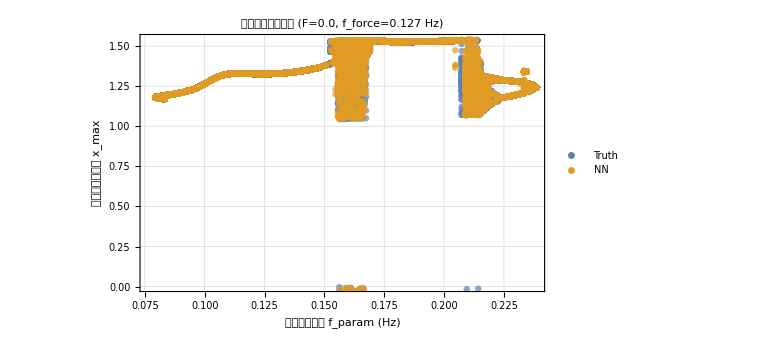

```mathematica
ClearAll[LocalMaxBifurcationParamSweep];

Options[LocalMaxBifurcationParamSweep]={"ForceFreq"->0.8/(2*Pi),(*外激励频率 (固定,Hz)*)"ForceAmplitude"->0.,(*外激励幅值 F (固定)*)"ParamFreqRange"->{0.5/(2*Pi),1.5/(2*Pi)},(*参数激励频率范围 (Hz)*)"ParamAmplitude"->0.4,(*参数激励幅值 κ (固定)*)"FreqPoints"->300,(*频率采样点数*)"TransientCycles"->100,(*瞬态周期数(丢弃)*)"SteadyCycles"->200,(*稳态周期数(采样)*)"InitialCondition"->{1.,0.},(*初始条件 {x0,v0}*)"PlotBoth"->True,(*是否同时绘制 NN 和 Truth*)"PlotVelocity"->False,(*True:绘制速度;False:绘制位移*)"ExportData"->True,(*是否导出数据*)"ExportPath"->"LocalMaxBifurcation_ParamSweep.xlsx" (*导出文件路径*)};

LocalMaxBifurcationParamSweep[OptionsPattern[]]:=Module[{freqForce,forceAmp,kappaParam,freqRange,nFreq,nTrans,nSteady,ic,plotBoth,plotV,freqs,results,makeData,plotData,colorTruth,colorNN,yLabel,exportData,exportPath},(*读取参数*)freqForce=OptionValue["ForceFreq"];
forceAmp=OptionValue["ForceAmplitude"];
kappaParam=OptionValue["ParamAmplitude"];
freqRange=OptionValue["ParamFreqRange"];
nFreq=OptionValue["FreqPoints"];
nTrans=OptionValue["TransientCycles"];
nSteady=OptionValue["SteadyCycles"];
ic=OptionValue["InitialCondition"];
plotBoth=OptionValue["PlotBoth"];
plotV=OptionValue["PlotVelocity"];
exportData=OptionValue["ExportData"];
exportPath=OptionValue["ExportPath"];
colorTruth=RGBColor[0.368,0.507,0.710];
colorNN=RGBColor[0.880,0.611,0.142];
(*生成频率点*)freqs=N@Range[freqRange[[1]],freqRange[[2]],(freqRange[[2]]-freqRange[[1]])/(nFreq-1)];
yLabel=If[plotV,"速度局部最大值 v_max","位移局部最大值 x_max"];
(*打印配置信息*)Print["🔄 正在计算局部最大值分岔图(扫描参数激励频率)..."];
Print["外激励: F = ",forceAmp,", f_force = ",NumberForm[freqForce,{4,3}]," Hz (固定)"];
Print["参数激励幅值: κ = ",kappaParam," (固定)"];
Print["参数激励频率范围: ",freqRange," Hz,共 ",nFreq," 个点"];
Print["瞬态周期: ",nTrans,",稳态周期: ",nSteady];
(*局部最大值提取函数*)makeData[solver_,label_]:=Module[{data={},sol,func,T,tTotal,tStart,localMaxVals,freqParam,timePoints,values,maxIndices},Monitor[Do[(*基于外激励和参数激励中的最高频率来确定周期*)T=1./Max[freqForce,freqParam];
tTotal=(nTrans+nSteady)*T;
tStart=nTrans*T;
(*求解:固定外激励,变化参数激励频率*)sol=solver[freqParam,kappaParam,ic[[1]],tTotal,ic[[2]],freqForce,forceAmp];
If[sol===$Failed,Print["⚠️ ",label," 在参数激励频率 ",NumberForm[freqParam,{4,3}]," Hz 处求解失败"];
Continue[]];
(*获取位移或速度函数*)func=If[plotV,x'/. sol,x/. sol];
(*在稳态区间内密集采样*)timePoints=Range[tStart,tTotal,0.01];(*每0.01秒采样一次*)values=func/@timePoints;
(*找到局部最大值的索引*)(*一个点是局部最大值,当且仅当它大于前后相邻的点*)maxIndices=Position[Table[If[i==1||i==Length[values],False,values[[i]]>values[[i-1]]&&values[[i]]>values[[i+1]]],{i,Length[values]}],True]//Flatten;
(*提取局部最大值*)localMaxVals=values[[maxIndices]];
(*存储 (参数激励频率,局部最大值) 对*)If[Length[localMaxVals]>0,data=Join[data,Transpose[{ConstantArray[freqParam,Length[localMaxVals]],localMaxVals}]]];,{freqParam,freqs}],Row[{ProgressIndicator[freqParam,freqRange],"  ",NumberForm[freqParam,{4,3}]," Hz"}]];
data];
(*计算 NN 和/或 Truth 数据*)If[plotBoth,Print["\n📊 计算 NN 系统..."];
results=<|"NN"->makeData[SolveNN,"NN"]|>;
Print["✅ NN 完成!共 ",Length[results["NN"]]," 个局部最大值"];
Print["\n📊 计算 Truth 系统..."];
results=Append[results,"Truth"->makeData[SolveTruth,"Truth"]];
Print["✅ Truth 完成!共 ",Length[results["Truth"]]," 个局部最大值"];
(*绘制对比图*)plotData=ListPlot[{results["Truth"],results["NN"]},PlotStyle->{Directive[colorTruth,PointSize[0.008],Opacity[0.7]],Directive[colorNN,PointSize[0.008],Opacity[0.7]]},PlotLegends->Placed[LineLegend[{Directive[colorTruth,PointSize[0.02]],Directive[colorNN,PointSize[0.02]]},{"Truth","NN"}],After],AxesLabel->{Style["参数激励频率 f_param (Hz)",14],Style[yLabel,14]},PlotLabel->Style[StringTemplate["局部最大值分岔图 (F=``, f_force=`` Hz)"][forceAmp,NumberForm[freqForce,{4,3}]],Bold,16],ImageSize->Large,Frame->True,GridLines->Automatic,AspectRatio->0.6];
(*导出数据*)If[exportData,Print["\n💾 正在导出数据到 ",exportPath,"..."];
Export[exportPath,{"Truth系统"->Prepend[results["Truth"],{"参数激励频率 (Hz)",yLabel}],"NN系统"->Prepend[results["NN"],{"参数激励频率 (Hz)",yLabel}],"参数信息"->{{"参数","值"},{"外激励频率 (Hz)",freqForce},{"外激励幅值 F",forceAmp},{"参数激励幅值 κ",kappaParam},{"参数激励频率范围起点 (Hz)",freqRange[[1]]},{"参数激励频率范围终点 (Hz)",freqRange[[2]]},{"频率采样点数",nFreq},{"瞬态周期数",nTrans},{"稳态周期数",nSteady},{"初始位移",ic[[1]]},{"初始速度",ic[[2]]},{"绘制变量",yLabel}}}];
Print["✅ 数据已成功导出到: ",exportPath];
Print["   - Truth系统: ",Length[results["Truth"]]," 个数据点"];
Print["   - NN系统: ",Length[results["NN"]]," 个数据点"];];,(*仅绘制 NN*)Print["\n📊 计算 NN 系统..."];
results=makeData[SolveNN,"NN"];
Print["✅ 完成!共 ",Length[results]," 个局部最大值"];
plotData=ListPlot[results,PlotStyle->Directive[colorNN,PointSize[0.008],Opacity[0.7]],AxesLabel->{Style["参数激励频率 f_param (Hz)",14],Style[yLabel,14]},PlotLabel->Style[StringTemplate["局部最大值分岔图 (NN, F=``, f_force=`` Hz)"][forceAmp,NumberForm[freqForce,{4,3}]],Bold,16],ImageSize->Large,Frame->True,GridLines->Automatic,AspectRatio->0.6];
(*导出数据*)If[exportData,Print["\n💾 正在导出数据到 ",exportPath,"..."];
Export[exportPath,{"NN系统"->Prepend[results,{"参数激励频率 (Hz)",yLabel}],"参数信息"->{{"参数","值"},{"外激励频率 (Hz)",freqForce},{"外激励幅值 F",forceAmp},{"参数激励幅值 κ",kappaParam},{"参数激励频率范围起点 (Hz)",freqRange[[1]]},{"参数激励频率范围终点 (Hz)",freqRange[[2]]},{"频率采样点数",nFreq},{"瞬态周期数",nTrans},{"稳态周期数",nSteady},{"初始位移",ic[[1]]},{"初始速度",ic[[2]]},{"绘制变量",yLabel}}}];
Print["✅ 数据已成功导出到: ",exportPath];
Print["   - NN系统: ",Length[results]," 个数据点"];];];
Print["\n✨ 局部最大值分岔图绘制完成!\n"];
plotData];

(* =======================使用示例=======================*)

(*示例:默认参数,固定外激励(F=0,f_force=0.8/2π Hz),扫描参数激励频率,同时绘制 NN 和 Truth,显示位移局部最大值,并导出数据*)
LocalMaxBifurcationParamSweep[]
```

```mathematica
ClearAll[ComputeLyapunovExponentForceFixed];

(*计算最大李雅普诺夫指数-固定外激励系统*)
ComputeLyapunovExponentForceFixed[freqForce_?NumericQ,force_?NumericQ,freqParam_?NumericQ,kappa_?NumericQ,x0_?NumericQ,nTransient_:100,nCompute_:100,systemType_:"NN",v0_:0.]:=Module[{T,tTrans,tCompute,x0Start,v0Start,sol,xFunc,vFunc,disturb=10^-3,solRef,solPert,xRef,vRef,xPert,vPert,dt,tList,distanceList,lyapunovTable,lambda},(*基于外激励和参数激励中的最高频率*)T=1/Max[freqForce,freqParam];
tTrans=nTransient*T;
tCompute=nCompute*T;
(*步骤1:积分到稳态*)sol=If[systemType=="NN",SolveNN[freqParam,kappa,x0,tTrans,v0,freqForce,force],SolveTruth[freqParam,kappa,x0,tTrans,v0,freqForce,force]];
If[sol===$Failed,Return[$Failed]];
xFunc=x/. sol;
vFunc=x'/. sol;
x0Start=xFunc[tTrans];
v0Start=vFunc[tTrans];
(*步骤2:从稳态开始，积分参考轨道和扰动轨道*)solRef=If[systemType=="NN",SolveNN[freqParam,kappa,x0Start,tCompute,v0Start,freqForce,force],SolveTruth[freqParam,kappa,x0Start,tCompute,v0Start,freqForce,force]];
If[solRef===$Failed,Return[$Failed]];
solPert=If[systemType=="NN",SolveNN[freqParam,kappa,x0Start+disturb,tCompute,v0Start,freqForce,force],SolveTruth[freqParam,kappa,x0Start+disturb,tCompute,v0Start,freqForce,force]];
If[solPert===$Failed,Return[$Failed]];
xRef=x/. solRef;
vRef=x'/. solRef;
xPert=x/. solPert;
vPert=x'/. solPert;
(*步骤3:在时间网格上计算距离*)dt=T/100;
tList=Range[dt,tCompute,dt];
distanceList=Table[Sqrt[(xPert[t]-xRef[t])^2+(vPert[t]-vRef[t])^2],{t,tList}];
(*检查数值稳定性*)If[Min[distanceList]<=0||Max[distanceList]>100,Return[$Failed]];
(*步骤4:计算李雅普诺夫指数*)lyapunovTable=Log[distanceList/disturb];
lambda=Total[lyapunovTable]/(Length[tList]*dt);
(*返回结果*){freqForce,force,freqParam,kappa,lambda}];

(*批量计算李雅普诺夫指数-固定外激励，扫描参数激励*)
ClearAll[BatchComputeLyapunovForceFixed];

BatchComputeLyapunovForceFixed[freqForce_?NumericQ,force_?NumericQ,freqParamList_,kappaList_,systemType_:"NN",x0_:1.,nTransient_:100,nCompute_:100,v0_:0.]:=Module[{results,total,current,startTime,freqParam,kappa,result,lambda,chaosType},results={};
total=Length[freqParamList]*Length[kappaList];
current=0;
startTime=AbsoluteTime[];
Print["开始批量计算 ",systemType," 系统（固定外激励）"];
Print["外激励: F = ",force,", f_force = ",NumberForm[freqForce,{4,3}]," Hz (固定)"];
Print["参数激励频率点数: ",Length[freqParamList]];
Print["参数激励幅值点数: ",Length[kappaList]];
Print["总计算点数: ",total];
Print["="~~StringRepeat["=",60]];
Do[Do[current++;
result=ComputeLyapunovExponentForceFixed[freqForce,force,freqParam,kappa,x0,nTransient,nCompute,systemType,v0];
If[result===$Failed,lambda="Failed";
chaosType="Failed",lambda=result[[5]];
(*判断混沌或周期*)chaosType=Which[lambda>0.01,"Chaos",lambda<-0.01,"Periodic",True,"Quasi-Periodic"]];
AppendTo[results,{freqParam,kappa,lambda,chaosType}];
(*进度显示*)If[Mod[current,100]==0||current==total,Print["进度: ",current,"/",total," (",NumberForm[100.*current/total,{4,1}],"%) | f_param=",NumberForm[freqParam,{4,3}],", κ=",NumberForm[kappa,{3,2}],", λ=",If[lambda==="Failed","Failed",NumberForm[lambda,{6,4}]]," | 用时: ",Round[AbsoluteTime[]-startTime,0.1],"s"]];,{kappa,kappaList}];,{freqParam,freqParamList}];
Print["="~~StringRepeat["=",60]];
Print["计算完成！总用时: ",Round[AbsoluteTime[]-startTime,0.1],"s"];
results];

(*导出到Excel-按类型分sheet*)
ClearAll[ExportToExcelByTypeForceFixed];

ExportToExcelByTypeForceFixed[results_,filename_,systemType_:"NN",freqForce_,force_]:=Module[{header,chaosData,periodicData,quasiData,failedData,chaosSheet,periodicSheet,quasiSheet,failedSheet,allSheet,metaSheet},(*创建表头*)header={"Param_Frequency (Hz)","Param_Amplitude_κ","Lyapunov_Exponent","Type"};
(*按类型分类数据*)chaosData=Select[results,#[[4]]=="Chaos"&];
periodicData=Select[results,#[[4]]=="Periodic"&];
quasiData=Select[results,#[[4]]=="Quasi-Periodic"&];
failedData=Select[results,#[[4]]=="Failed"&];
(*创建各个sheet的数据（带表头）*)chaosSheet=Prepend[chaosData,header];
periodicSheet=Prepend[periodicData,header];
quasiSheet=Prepend[quasiData,header];
failedSheet=Prepend[failedData,header];
allSheet=Prepend[results,header];
(*元数据*)metaSheet={{"参数","值"},{"系统类型",systemType},{"外激励频率 (Hz)",freqForce},{"外激励幅值 F",force},{"",""},{"统计信息",""},{"混沌点数",Length[chaosData]},{"周期点数",Length[periodicData]},{"准周期点数",Length[quasiData]},{"失败点数",Length[failedData]},{"总点数",Length[results]}};
(*导出到Excel*)Export[filename,{"Chaos"->chaosSheet,"Periodic"->periodicSheet,"Quasi-Periodic"->quasiSheet,"Failed"->failedSheet,"All Data"->allSheet,"Metadata"->metaSheet},"XLSX"];
(*打印统计信息*)Print["数据已导出到: ",filename];
Print["  Sheet 'Chaos': ",Length[chaosData]," 条数据"];
Print["  Sheet 'Periodic': ",Length[periodicData]," 条数据"];
Print["  Sheet 'Quasi-Periodic': ",Length[quasiData]," 条数据"];
Print["  Sheet 'Failed': ",Length[failedData]," 条数据"];
Print["  Sheet 'All Data': ",Length[results]," 条数据"];
Print["  Sheet 'Metadata': 参数信息"];
Print["总数据行数: ",Length[results]];];

(* ====================主程序====================*)

(*设置外激励（固定）*)
freqForce=0/(2*Pi);  (*外激励频率*)
force=0.;             (*外激励幅值*)

(*设置扫描参数*)
(*参数激励频率范围*)
freqParamList=Range[0.5/(2*Pi),1.5/(2*Pi),0.01/(2*Pi)];

(*参数激励幅值范围*)
kappaList=Range[0.1,0.5,0.005];

Print["="~~StringRepeat["=",70]];
Print["参数设置"];
Print["="~~StringRepeat["=",70]];
Print["外激励频率: ",NumberForm[freqForce,{4,3}]," Hz (固定)"];
Print["外激励幅值: ",force," (固定)"];
Print["参数激励频率列表: ",Length[freqParamList]," 个点"];
Print["参数激励幅值列表: ",Length[kappaList]," 个点"];
Print["总计算点数: ",Length[freqParamList]*Length[kappaList]];
Print["\n"];

(*计算NN系统*)
Print["="~~StringRepeat["=",70]];
Print["开始计算神经网络系统 (NN)"];
Print["="~~StringRepeat["=",70]];
resultsNN=BatchComputeLyapunovForceFixed[freqForce,force,freqParamList,kappaList,"NN",1,20,30,0.];

(*导出NN系统结果*)
ExportToExcelByTypeForceFixed[resultsNN,"Lyapunov_NN_ForceFixed_Results.xlsx","NN",freqForce,force];

Print["\n\n"];

(*计算Truth系统*)
Print["="~~StringRepeat["=",70]];
Print["开始计算真实系统 (Truth)"];
Print["="~~StringRepeat["=",70]];
resultsTruth=BatchComputeLyapunovForceFixed[freqForce,force,freqParamList,kappaList,"Truth",1,20,30,0.];

(*导出Truth系统结果*)
ExportToExcelByTypeForceFixed[resultsTruth,"Lyapunov_Truth_ForceFixed_Results.xlsx","Truth",freqForce,force];

(*生成对比分析*)
Print["\n\n"];
Print["="~~StringRepeat["=",70]];
Print["系统对比分析"];
Print["="~~StringRepeat["=",70]];

(*创建对比表*)
ClearAll[CreateComparisonTableForceFixed];
CreateComparisonTableForceFixed[resultsNN_,resultsTruth_]:=Module[{comparison,nn,truth,diffLambda,diffType},comparison={};
Do[nn=resultsNN[[i]];
truth=resultsTruth[[i]];
diffLambda=If[nn[[3]]==="Failed"||truth[[3]]==="Failed","N/A",nn[[3]]-truth[[3]]];
diffType=If[nn[[4]]==truth[[4]],"Match","Mismatch"];
AppendTo[comparison,{nn[[1]],nn[[2]],nn[[3]],nn[[4]],truth[[3]],truth[[4]],diffLambda,diffType}];,{i,Length[resultsNN]}];
comparison];

comparisonData=CreateComparisonTableForceFixed[resultsNN,resultsTruth];

(*导出对比结果*)
ClearAll[ExportComparisonToExcelForceFixed];
ExportComparisonToExcelForceFixed[comparisonData_,freqForce_,force_]:=Module[{header,matchData,mismatchData,matchSheet,mismatchSheet,allSheet,metaSheet},(*创建表头*)header={"Param_Frequency (Hz)","Param_Amplitude_κ","Lambda_NN","Type_NN","Lambda_Truth","Type_Truth","Lambda_Diff","Type_Match"};
(*按匹配情况分类*)matchData=Select[comparisonData,#[[8]]=="Match"&];
mismatchData=Select[comparisonData,#[[8]]=="Mismatch"&];
(*创建各sheet数据*)matchSheet=Prepend[matchData,header];
mismatchSheet=Prepend[mismatchData,header];
allSheet=Prepend[comparisonData,header];
(*元数据*)metaSheet={{"参数","值"},{"外激励频率 (Hz)",freqForce},{"外激励幅值 F",force},{"",""},{"统计信息",""},{"类型匹配点数",Length[matchData]},{"类型不匹配点数",Length[mismatchData]},{"总点数",Length[comparisonData]},{"匹配率 (%)",100.*Length[matchData]/Length[comparisonData]}};
(*导出*)Export["Lyapunov_ForceFixed_Comparison.xlsx",{"Match"->matchSheet,"Mismatch"->mismatchSheet,"All Comparison"->allSheet,"Metadata"->metaSheet},"XLSX"];
Print["对比数据已导出到: Lyapunov_ForceFixed_Comparison.xlsx"];
Print["  Sheet 'Match': ",Length[matchData]," 条数据"];
Print["  Sheet 'Mismatch': ",Length[mismatchData]," 条数据"];
Print["  Sheet 'All Comparison': ",Length[comparisonData]," 条数据"];
Print["  Sheet 'Metadata': 参数信息"];
Print["类型匹配率: ",NumberForm[100.*Length[matchData]/Length[comparisonData],{5,2}],"%"];];

ExportComparisonToExcelForceFixed[comparisonData,freqForce,force];

Print["\n✅ 所有计算和导出完成！"];
```

=======================================================================

参数设置

=======================================================================

外激励频率: 0 Hz (固定)

外激励幅值: 0. (固定)

参数激励频率列表: 101 个点

参数激励幅值列表: 81 个点

总计算点数: 8181

=======================================================================

开始计算神经网络系统 (NN)

=======================================================================

开始批量计算 NN 系统（固定外激励）

外激励: F = 0., f_force = 0 Hz (固定)

参数激励频率点数: 101

参数激励幅值点数: 81

总计算点数: 8181

=============================================================

进度: 100/8181 (1.2%) | f_param=0.081, κ=0.19, λ=-63.3205 | 用时: 1608.8s

进度: 200/8181 (2.4%) | f_param=0.083, κ=0.29, λ=-64.7728 | 用时: 3201.8s

进度: 300/8181 (3.7%) | f_param=0.084, κ=0.38, λ=-66.2835 | 用时: 4771.s

进度: 400/8181 (4.9%) | f_param=0.086, κ=0.48, λ=-66.3687 | 用时: 6320.3s

进度: 500/8181 (6.1%) | f_param=0.089, κ=0.17, λ=-68.2393 | 用时: 7797.8s

进度: 600/8181 (7.3%) | f_param=0.091, κ=0.26, λ=-70.8970 | 用时: 9242.4s

进度: 700/8181 (8.6%) | f_param=0.092, κ=0.36, λ=-71.3608 | 用时: 10701.2s

进度: 800/8181 (9.8%) | f_param=0.094, κ=0.45, λ=-72.1428 | 用时: 12141.1s

进度: 900/8181 (11.0%) | f_param=0.097, κ=0.14, λ=-75.8332 | 用时: 13554.s

进度: 1000/8181 (12.2%) | f_param=0.099, κ=0.24, λ=-76.6765 | 用时: 14936.9s

进度: 1100/8181 (13.4%) | f_param=0.100, κ=0.33, λ=-77.2612 | 用时: 16327.2s

进度: 1200/8181 (14.7%) | f_param=0.102, κ=0.43, λ=-75.7306 | 用时: 17714.7s

进度: 1300/8181 (15.9%) | f_param=0.105, κ=0.12, λ=-79.2079 | 用时: 19096.8s

进度: 1400/8181 (17.1%) | f_param=0.107, κ=0.21, λ=-81.0803 | 用时: 20418.1s

进度: 1500/8181 (18.3%) | f_param=0.108, κ=0.31, λ=-83.7088 | 用时: 21749.4s

进度: 1600/8181 (19.6%) | f_param=0.110, κ=0.40, λ=-83.7823 | 用时: 23080.6s

进度: 1700/8181 (20.8%) | f_param=0.111, κ=0.50, λ=-83.3493 | 用时: 24403.7s

进度: 1800/8181 (22.0%) | f_param=0.115, κ=0.19, λ=-86.8742 | 用时: 25663.3s

进度: 1900/8181 (23.2%) | f_param=0.116, κ=0.28, λ=-87.3653 | 用时: 26921.5s

进度: 2000/8181 (24.4%) | f_param=0.118, κ=0.38, λ=-88.4231 | 用时: 28156.5s

进度: 2100/8181 (25.7%) | f_param=0.119, κ=0.47, λ=-87.0683 | 用时: 29389.s

进度: 2200/8181 (26.9%) | f_param=0.123, κ=0.16, λ=-92.3092 | 用时: 30563.4s

进度: 2300/8181 (28.1%) | f_param=0.124, κ=0.26, λ=-89.7159 | 用时: 31725.5s

进度: 2400/8181 (29.3%) | f_param=0.126, κ=0.35, λ=-94.1745 | 用时: 32873.8s

进度: 2500/8181 (30.6%) | f_param=0.127, κ=0.45, λ=-94.2235 | 用时: 34015.2s

进度: 2600/8181 (31.8%) | f_param=0.131, κ=0.14, λ=-95.5677 | 用时: 35139.4s

进度: 2700/8181 (33.0%) | f_param=0.132, κ=0.23, λ=-98.0713 | 用时: 36230.3s

进度: 2800/8181 (34.2%) | f_param=0.134, κ=0.33, λ=-97.4279 | 用时: 37308.7s

进度: 2900/8181 (35.4%) | f_param=0.135, κ=0.42, λ=-100.8510 | 用时: 38395.5s

进度: 3000/8181 (36.7%) | f_param=0.138, κ=0.11, λ=-102.8260 | 用时: 39468.2s

进度: 3100/8181 (37.9%) | f_param=0.140, κ=0.21, λ=-104.4930 | 用时: 40521.4s

进度: 3200/8181 (39.1%) | f_param=0.142, κ=0.30, λ=-102.3610 | 用时: 41570.5s

进度: 3300/8181 (40.3%) | f_param=0.143, κ=0.40, λ=-103.0810 | 用时: 42618.5s

进度: 3400/8181 (41.6%) | f_param=0.145, κ=0.49, λ=-102.6610 | 用时: 43661.3s

进度: 3500/8181 (42.8%) | f_param=0.148, κ=0.18, λ=-107.3310 | 用时: 44687.7s

进度: 3600/8181 (44.0%) | f_param=0.150, κ=0.28, λ=-107.2440 | 用时: 45715.9s

进度: 3700/8181 (45.2%) | f_param=0.151, κ=0.37, λ=-106.8580 | 用时: 46734.1s

进度: 3800/8181 (46.4%) | f_param=0.153, κ=0.47, λ=80.6701 | 用时: 47765.7s

进度: 3900/8181 (47.7%) | f_param=0.156, κ=0.16, λ=-111.9910 | 用时: 48786.6s

进度: 4000/8181 (48.9%) | f_param=0.158, κ=0.25, λ=-113.5780 | 用时: 49811.4s

进度: 4100/8181 (50.1%) | f_param=0.159, κ=0.35, λ=-91.9571 | 用时: 50826.1s

进度: 4200/8181 (51.3%) | f_param=0.161, κ=0.44, λ=101.2180 | 用时: 51831.1s

进度: 4300/8181 (52.6%) | f_param=0.164, κ=0.13, λ=-116.2590 | 用时: 52794.3s

进度: 4400/8181 (53.8%) | f_param=0.166, κ=0.23, λ=-115.7990 | 用时: 53807.4s

进度: 4500/8181 (55.0%) | f_param=0.167, κ=0.32, λ=100.1210 | 用时: 54811.3s

进度: 4600/8181 (56.2%) | f_param=0.169, κ=0.42, λ=87.3972 | 用时: 55824.9s

进度: 4700/8181 (57.5%) | f_param=0.172, κ=0.11, λ=-119.3910 | 用时: 56817.6s

进度: 4800/8181 (58.7%) | f_param=0.173, κ=0.20, λ=-120.7580 | 用时: 57839.3s

进度: 4900/8181 (59.9%) | f_param=0.175, κ=0.30, λ=-3.1081 | 用时: 58855.5s

进度: 5000/8181 (61.1%) | f_param=0.177, κ=0.39, λ=-24.7471 | 用时: 59884.6s

进度: 5100/8181 (62.3%) | f_param=0.178, κ=0.49, λ=98.1913 | 用时: 60899.8s

进度: 5200/8181 (63.6%) | f_param=0.181, κ=0.18, λ=-125.5710 | 用时: 61897.9s

进度: 5300/8181 (64.8%) | f_param=0.183, κ=0.27, λ=-115.2360 | 用时: 62919.7s

进度: 5400/8181 (66.0%) | f_param=0.185, κ=0.37, λ=91.9294 | 用时: 63946.2s

进度: 5500/8181 (67.2%) | f_param=0.186, κ=0.46, λ=-102.8560 | 用时: 64987.1s

进度: 5600/8181 (68.5%) | f_param=0.189, κ=0.15, λ=-129.0380 | 用时: 66008.7s

进度: 5700/8181 (69.7%) | f_param=0.191, κ=0.25, λ=-123.7720 | 用时: 67030.7s

进度: 5800/8181 (70.9%) | f_param=0.193, κ=0.34, λ=97.9829 | 用时: 68056.2s

进度: 5900/8181 (72.1%) | f_param=0.194, κ=0.44, λ=-110.1060 | 用时: 69065.8s

进度: 6000/8181 (73.3%) | f_param=0.197, κ=0.13, λ=-123.7490 | 用时: 70080.5s

进度: 6100/8181 (74.6%) | f_param=0.199, κ=0.22, λ=-132.0670 | 用时: 71070.s

进度: 6200/8181 (75.8%) | f_param=0.201, κ=0.32, λ=-25.7351 | 用时: 72062.5s

进度: 6300/8181 (77.0%) | f_param=0.202, κ=0.41, λ=-127.8120 | 用时: 73036.s

进度: 6400/8181 (78.2%) | f_param=0.205, κ=0.10, λ=-128.8350 | 用时: 74001.2s

进度: 6500/8181 (79.5%) | f_param=0.207, κ=0.20, λ=-136.6930 | 用时: 74852.2s

进度: 6600/8181 (80.7%) | f_param=0.208, κ=0.29, λ=-136.1170 | 用时: 75699.7s

进度: 6700/8181 (81.9%) | f_param=0.210, κ=0.39, λ=89.6145 | 用时: 76531.3s

进度: 6800/8181 (83.1%) | f_param=0.212, κ=0.48, λ=-131.3300 | 用时: 77362.7s

进度: 6900/8181 (84.3%) | f_param=0.215, κ=0.17, λ=-138.9230 | 用时: 78208.4s

进度: 7000/8181 (85.6%) | f_param=0.216, κ=0.27, λ=-142.2870 | 用时: 79130.s

进度: 7100/8181 (86.8%) | f_param=0.218, κ=0.36, λ=-104.1990 | 用时: 80041.8s

进度: 7200/8181 (88.0%) | f_param=0.220, κ=0.46, λ=136.7680 | 用时: 80951.6s

进度: 7300/8181 (89.2%) | f_param=0.223, κ=0.15, λ=-148.3740 | 用时: 81852.2s

进度: 7400/8181 (90.5%) | f_param=0.224, κ=0.24, λ=-149.1540 | 用时: 82740.4s

进度: 7500/8181 (91.7%) | f_param=0.226, κ=0.34, λ=-140.8280 | 用时: 83625.2s

进度: 7600/8181 (92.9%) | f_param=0.228, κ=0.43, λ=-145.1060 | 用时: 84508.1s

进度: 7700/8181 (94.1%) | f_param=0.231, κ=0.12, λ=-151.6940 | 用时: 85389.5s

进度: 7800/8181 (95.3%) | f_param=0.232, κ=0.22, λ=-154.1620 | 用时: 86253.9s

进度: 7900/8181 (96.6%) | f_param=0.234, κ=0.31, λ=-152.5060 | 用时: 87117.3s

进度: 8000/8181 (97.8%) | f_param=0.236, κ=0.41, λ=-97.3674 | 用时: 87972.8s

进度: 8100/8181 (99.0%) | f_param=0.237, κ=0.50, λ=-30.3702 | 用时: 88823.1s

进度: 8181/8181 (100.0%) | f_param=0.239, κ=0.50, λ=-146.1330 | 用时: 89507.8s

=============================================================

计算完成！总用时: 89507.8s

数据已导出到: Lyapunov_NN_ForceFixed_Results.xlsx

Sheet 'Chaos': 974 条数据

Sheet 'Periodic': 7207 条数据

Sheet 'Quasi-Periodic': 0 条数据

Sheet 'Failed': 0 条数据

Sheet 'All Data': 8181 条数据

Sheet 'Metadata': 参数信息

总数据行数: 8181

=======================================================================

开始计算真实系统 (Truth)

=======================================================================

开始批量计算 Truth 系统（固定外激励）

外激励: F = 0., f_force = 0 Hz (固定)

参数激励频率点数: 101

参数激励幅值点数: 81

总计算点数: 8181

=============================================================

进度: 100/8181 (1.2%) | f_param=0.081, κ=0.19, λ=-75.1857 | 用时: 3.8s

进度: 200/8181 (2.4%) | f_param=0.083, κ=0.29, λ=-72.4335 | 用时: 7.5s

进度: 300/8181 (3.7%) | f_param=0.084, κ=0.38, λ=-74.5467 | 用时: 11.4s

进度: 400/8181 (4.9%) | f_param=0.086, κ=0.48, λ=-75.5452 | 用时: 15.2s

进度: 500/8181 (6.1%) | f_param=0.089, κ=0.17, λ=-80.6763 | 用时: 18.9s

进度: 600/8181 (7.3%) | f_param=0.091, κ=0.26, λ=-79.3237 | 用时: 22.8s

进度: 700/8181 (8.6%) | f_param=0.092, κ=0.36, λ=-81.9070 | 用时: 26.4s

进度: 800/8181 (9.8%) | f_param=0.094, κ=0.45, λ=-79.8546 | 用时: 30.1s

进度: 900/8181 (11.0%) | f_param=0.097, κ=0.14, λ=-87.2631 | 用时: 33.8s

进度: 1000/8181 (12.2%) | f_param=0.099, κ=0.24, λ=-83.1928 | 用时: 37.4s

进度: 1100/8181 (13.4%) | f_param=0.100, κ=0.33, λ=-86.4439 | 用时: 41.3s

进度: 1200/8181 (14.7%) | f_param=0.102, κ=0.43, λ=-84.3387 | 用时: 44.8s

进度: 1300/8181 (15.9%) | f_param=0.105, κ=0.12, λ=-94.3580 | 用时: 48.5s

进度: 1400/8181 (17.1%) | f_param=0.107, κ=0.21, λ=-90.7270 | 用时: 51.9s

进度: 1500/8181 (18.3%) | f_param=0.108, κ=0.31, λ=-89.5148 | 用时: 55.5s

进度: 1600/8181 (19.6%) | f_param=0.110, κ=0.40, λ=-91.6379 | 用时: 59.s

进度: 1700/8181 (20.8%) | f_param=0.111, κ=0.50, λ=-89.4442 | 用时: 62.5s

进度: 1800/8181 (22.0%) | f_param=0.115, κ=0.19, λ=-98.3731 | 用时: 65.9s

进度: 1900/8181 (23.2%) | f_param=0.116, κ=0.28, λ=-97.7942 | 用时: 69.3s

进度: 2000/8181 (24.4%) | f_param=0.118, κ=0.38, λ=-101.2700 | 用时: 72.8s

进度: 2100/8181 (25.7%) | f_param=0.119, κ=0.47, λ=-99.3584 | 用时: 76.3s

进度: 2200/8181 (26.9%) | f_param=0.123, κ=0.16, λ=-102.8210 | 用时: 79.4s

进度: 2300/8181 (28.1%) | f_param=0.124, κ=0.26, λ=-103.9220 | 用时: 82.5s

进度: 2400/8181 (29.3%) | f_param=0.126, κ=0.35, λ=-103.1000 | 用时: 85.6s

进度: 2500/8181 (30.6%) | f_param=0.127, κ=0.45, λ=-101.2270 | 用时: 88.7s

进度: 2600/8181 (31.8%) | f_param=0.131, κ=0.14, λ=-107.8730 | 用时: 91.9s

进度: 2700/8181 (33.0%) | f_param=0.132, κ=0.23, λ=-108.7660 | 用时: 95.s

进度: 2800/8181 (34.2%) | f_param=0.134, κ=0.33, λ=-110.2720 | 用时: 98.1s

进度: 2900/8181 (35.4%) | f_param=0.135, κ=0.42, λ=-113.5210 | 用时: 101.2s

进度: 3000/8181 (36.7%) | f_param=0.138, κ=0.11, λ=-115.9200 | 用时: 104.4s

进度: 3100/8181 (37.9%) | f_param=0.140, κ=0.21, λ=-112.6670 | 用时: 107.6s

进度: 3200/8181 (39.1%) | f_param=0.142, κ=0.30, λ=-114.3360 | 用时: 110.8s

进度: 3300/8181 (40.3%) | f_param=0.143, κ=0.40, λ=-112.9260 | 用时: 114.s

进度: 3400/8181 (41.6%) | f_param=0.145, κ=0.49, λ=-111.9100 | 用时: 117.1s

进度: 3500/8181 (42.8%) | f_param=0.148, κ=0.18, λ=-115.6700 | 用时: 120.2s

进度: 3600/8181 (44.0%) | f_param=0.150, κ=0.28, λ=-120.7040 | 用时: 123.4s

进度: 3700/8181 (45.2%) | f_param=0.151, κ=0.37, λ=-118.1970 | 用时: 126.7s

进度: 3800/8181 (46.4%) | f_param=0.153, κ=0.47, λ=63.5080 | 用时: 130.1s

进度: 3900/8181 (47.7%) | f_param=0.156, κ=0.16, λ=-120.4740 | 用时: 133.3s

进度: 4000/8181 (48.9%) | f_param=0.158, κ=0.25, λ=-122.7850 | 用时: 136.7s

进度: 4100/8181 (50.1%) | f_param=0.159, κ=0.35, λ=-121.2090 | 用时: 139.9s

进度: 4200/8181 (51.3%) | f_param=0.161, κ=0.44, λ=90.4161 | 用时: 143.2s

进度: 4300/8181 (52.6%) | f_param=0.164, κ=0.13, λ=-130.7700 | 用时: 147.1s

进度: 4400/8181 (53.8%) | f_param=0.166, κ=0.23, λ=-129.4410 | 用时: 150.2s

进度: 4500/8181 (55.0%) | f_param=0.167, κ=0.32, λ=30.7497 | 用时: 153.6s

进度: 4600/8181 (56.2%) | f_param=0.169, κ=0.42, λ=100.9300 | 用时: 156.9s

进度: 4700/8181 (57.5%) | f_param=0.172, κ=0.11, λ=-137.2960 | 用时: 160.1s

进度: 4800/8181 (58.7%) | f_param=0.173, κ=0.20, λ=-132.4710 | 用时: 163.1s

进度: 4900/8181 (59.9%) | f_param=0.175, κ=0.30, λ=1.3268 | 用时: 166.3s

进度: 5000/8181 (61.1%) | f_param=0.177, κ=0.39, λ=-26.3065 | 用时: 169.6s

进度: 5100/8181 (62.3%) | f_param=0.178, κ=0.49, λ=100.4690 | 用时: 172.7s

进度: 5200/8181 (63.6%) | f_param=0.181, κ=0.18, λ=-137.7230 | 用时: 175.9s

进度: 5300/8181 (64.8%) | f_param=0.183, κ=0.27, λ=-119.6150 | 用时: 179.1s

进度: 5400/8181 (66.0%) | f_param=0.185, κ=0.37, λ=111.1360 | 用时: 182.2s

进度: 5500/8181 (67.2%) | f_param=0.186, κ=0.46, λ=-44.8589 | 用时: 185.3s

进度: 5600/8181 (68.5%) | f_param=0.189, κ=0.15, λ=-134.5720 | 用时: 188.4s

进度: 5700/8181 (69.7%) | f_param=0.191, κ=0.25, λ=-134.5130 | 用时: 191.4s

进度: 5800/8181 (70.9%) | f_param=0.193, κ=0.34, λ=89.6902 | 用时: 194.5s

进度: 5900/8181 (72.1%) | f_param=0.194, κ=0.44, λ=-110.4600 | 用时: 197.6s

进度: 6000/8181 (73.3%) | f_param=0.197, κ=0.13, λ=-132.0960 | 用时: 200.7s

进度: 6100/8181 (74.6%) | f_param=0.199, κ=0.22, λ=-141.8000 | 用时: 203.9s

进度: 6200/8181 (75.8%) | f_param=0.201, κ=0.32, λ=-26.3776 | 用时: 207.2s

进度: 6300/8181 (77.0%) | f_param=0.202, κ=0.41, λ=-125.6670 | 用时: 210.2s

进度: 6400/8181 (78.2%) | f_param=0.205, κ=0.10, λ=-136.5390 | 用时: 213.3s

进度: 6500/8181 (79.5%) | f_param=0.207, κ=0.20, λ=-150.6810 | 用时: 216.5s

进度: 6600/8181 (80.7%) | f_param=0.208, κ=0.29, λ=-169.9370 | 用时: 219.5s

进度: 6700/8181 (81.9%) | f_param=0.210, κ=0.39, λ=113.0170 | 用时: 222.5s

进度: 6800/8181 (83.1%) | f_param=0.212, κ=0.48, λ=143.2580 | 用时: 225.6s

进度: 6900/8181 (84.3%) | f_param=0.215, κ=0.17, λ=-147.1480 | 用时: 228.7s

进度: 7000/8181 (85.6%) | f_param=0.216, κ=0.27, λ=-149.7700 | 用时: 231.8s

进度: 7100/8181 (86.8%) | f_param=0.218, κ=0.36, λ=-125.0950 | 用时: 234.8s

进度: 7200/8181 (88.0%) | f_param=0.220, κ=0.46, λ=-150.6280 | 用时: 238.s

进度: 7300/8181 (89.2%) | f_param=0.223, κ=0.15, λ=-168.3160 | 用时: 241.s

进度: 7400/8181 (90.5%) | f_param=0.224, κ=0.24, λ=-157.1670 | 用时: 244.2s

进度: 7500/8181 (91.7%) | f_param=0.226, κ=0.34, λ=-155.4680 | 用时: 247.2s

进度: 7600/8181 (92.9%) | f_param=0.228, κ=0.43, λ=-158.5020 | 用时: 250.3s

进度: 7700/8181 (94.1%) | f_param=0.231, κ=0.12, λ=-170.7100 | 用时: 253.2s

进度: 7800/8181 (95.3%) | f_param=0.232, κ=0.22, λ=-167.3960 | 用时: 256.1s

进度: 7900/8181 (96.6%) | f_param=0.234, κ=0.31, λ=-159.9720 | 用时: 259.1s

进度: 8000/8181 (97.8%) | f_param=0.236, κ=0.41, λ=-141.0980 | 用时: 262.1s

进度: 8100/8181 (99.0%) | f_param=0.237, κ=0.50, λ=-160.8560 | 用时: 265.3s

进度: 8181/8181 (100.0%) | f_param=0.239, κ=0.50, λ=-165.1410 | 用时: 267.7s

=============================================================

计算完成！总用时: 267.7s

数据已导出到: Lyapunov_Truth_ForceFixed_Results.xlsx

Sheet 'Chaos': 985 条数据

Sheet 'Periodic': 7196 条数据

Sheet 'Quasi-Periodic': 0 条数据

Sheet 'Failed': 0 条数据

Sheet 'All Data': 8181 条数据

Sheet 'Metadata': 参数信息

总数据行数: 8181

=======================================================================

系统对比分析

=======================================================================

对比数据已导出到: Lyapunov_ForceFixed_Comparison.xlsx

Sheet 'Match': 7912 条数据

Sheet 'Mismatch': 269 条数据

Sheet 'All Comparison': 8181 条数据

Sheet 'Metadata': 参数信息

类型匹配率: 96.71%

✅ 所有计算和导出完成！

```mathematica
ClearAll[ComputeLyapunovExponentParam];

(*计算最大李雅普诺夫指数-参数激励系统*)
ComputeLyapunovExponentParam[freqParam_?NumericQ,kappa_?NumericQ,freqForce_?NumericQ,force_?NumericQ,x0_?NumericQ,nTransient_:100,nCompute_:100,systemType_:"NN",v0_:0.]:=Module[{T,tTrans,tCompute,x0Start,v0Start,sol,xFunc,vFunc,disturb=10^-3,solRef,solPert,xRef,vRef,xPert,vPert,dt,tList,distanceList,lyapunovTable,lambda},(*基于外激励和参数激励中的最高频率*)T=1/Max[freqForce,freqParam];
tTrans=nTransient*T;
tCompute=nCompute*T;
(*步骤1:积分到稳态*)sol=If[systemType=="NN",SolveNN[freqParam,kappa,x0,tTrans,v0,freqForce,force],SolveTruth[freqParam,kappa,x0,tTrans,v0,freqForce,force]];
If[sol===$Failed,Return[$Failed]];
xFunc=x/. sol;
vFunc=x'/. sol;
x0Start=xFunc[tTrans];
v0Start=vFunc[tTrans];
(*步骤2:从稳态开始，积分参考轨道和扰动轨道*)solRef=If[systemType=="NN",SolveNN[freqParam,kappa,x0Start,tCompute,v0Start,freqForce,force],SolveTruth[freqParam,kappa,x0Start,tCompute,v0Start,freqForce,force]];
If[solRef===$Failed,Return[$Failed]];
solPert=If[systemType=="NN",SolveNN[freqParam,kappa,x0Start+disturb,tCompute,v0Start,freqForce,force],SolveTruth[freqParam,kappa,x0Start+disturb,tCompute,v0Start,freqForce,force]];
If[solPert===$Failed,Return[$Failed]];
xRef=x/. solRef;
vRef=x'/. solRef;
xPert=x/. solPert;
vPert=x'/. solPert;
(*步骤3:在时间网格上计算距离*)dt=T/100;
tList=Range[dt,tCompute,dt];
distanceList=Table[Sqrt[(xPert[t]-xRef[t])^2+(vPert[t]-vRef[t])^2],{t,tList}];
(*检查数值稳定性*)If[Min[distanceList]<=0||Max[distanceList]>100,Return[$Failed]];
(*步骤4:计算李雅普诺夫指数*)lyapunovTable=Log[distanceList/disturb];
lambda=Total[lyapunovTable]/(Length[tList]*dt);
(*返回结果*){freqParam,kappa,freqForce,force,lambda}];

(*批量计算李雅普诺夫指数-固定参数激励，扫描外激励*)
ClearAll[BatchComputeLyapunovParamFixed];

BatchComputeLyapunovParamFixed[freqParam_?NumericQ,kappa_?NumericQ,freqForceList_,forceList_,systemType_:"NN",x0_:1.,nTransient_:100,nCompute_:100,v0_:0.]:=Module[{results,total,current,startTime,freqForce,force,result,lambda,chaosType},results={};
total=Length[freqForceList]*Length[forceList];
current=0;
startTime=AbsoluteTime[];
Print["开始批量计算 ",systemType," 系统（固定参数激励）"];
Print["参数激励: κ = ",kappa,", f_param = ",NumberForm[freqParam,{4,3}]," Hz (固定)"];
Print["外激励频率点数: ",Length[freqForceList]];
Print["外激励幅值点数: ",Length[forceList]];
Print["总计算点数: ",total];
Print["="~~StringRepeat["=",60]];
Do[Do[current++;
result=ComputeLyapunovExponentParam[freqParam,kappa,freqForce,force,x0,nTransient,nCompute,systemType,v0];
If[result===$Failed,lambda="Failed";
chaosType="Failed",lambda=result[[5]];
(*判断混沌或周期*)chaosType=Which[lambda>0.01,"Chaos",lambda<-0.01,"Periodic",True,"Quasi-Periodic"]];
AppendTo[results,{freqForce,force,lambda,chaosType}];
(*进度显示*)If[Mod[current,10]==0||current==total,Print["进度: ",current,"/",total," (",NumberForm[100.*current/total,{4,1}],"%) | f_force=",NumberForm[freqForce,{4,3}],", F=",NumberForm[force,{3,2}],", λ=",If[lambda==="Failed","Failed",NumberForm[lambda,{6,4}]]," | 用时: ",Round[AbsoluteTime[]-startTime,0.1],"s"]];,{force,forceList}];,{freqForce,freqForceList}];
Print["="~~StringRepeat["=",60]];
Print["计算完成！总用时: ",Round[AbsoluteTime[]-startTime,0.1],"s"];
results];

(*导出到Excel-按类型分sheet*)
ClearAll[ExportToExcelByTypeParam];

ExportToExcelByTypeParam[results_,filename_,systemType_:"NN",freqParam_,kappa_]:=Module[{header,chaosData,periodicData,quasiData,failedData,chaosSheet,periodicSheet,quasiSheet,failedSheet,allSheet,metaSheet},(*创建表头*)header={"Force_Frequency (Hz)","Force_Amplitude","Lyapunov_Exponent","Type"};
(*按类型分类数据*)chaosData=Select[results,#[[4]]=="Chaos"&];
periodicData=Select[results,#[[4]]=="Periodic"&];
quasiData=Select[results,#[[4]]=="Quasi-Periodic"&];
failedData=Select[results,#[[4]]=="Failed"&];
(*创建各个sheet的数据（带表头）*)chaosSheet=Prepend[chaosData,header];
periodicSheet=Prepend[periodicData,header];
quasiSheet=Prepend[quasiData,header];
failedSheet=Prepend[failedData,header];
allSheet=Prepend[results,header];
(*元数据*)metaSheet={{"参数","值"},{"系统类型",systemType},{"参数激励频率 (Hz)",freqParam},{"参数激励幅值 κ",kappa},{"",""},{"统计信息",""},{"混沌点数",Length[chaosData]},{"周期点数",Length[periodicData]},{"准周期点数",Length[quasiData]},{"失败点数",Length[failedData]},{"总点数",Length[results]}};
(*导出到Excel*)Export[filename,{"Chaos"->chaosSheet,"Periodic"->periodicSheet,"Quasi-Periodic"->quasiSheet,"Failed"->failedSheet,"All Data"->allSheet,"Metadata"->metaSheet},"XLSX"];
(*打印统计信息*)Print["数据已导出到: ",filename];
Print["  Sheet 'Chaos': ",Length[chaosData]," 条数据"];
Print["  Sheet 'Periodic': ",Length[periodicData]," 条数据"];
Print["  Sheet 'Quasi-Periodic': ",Length[quasiData]," 条数据"];
Print["  Sheet 'Failed': ",Length[failedData]," 条数据"];
Print["  Sheet 'All Data': ",Length[results]," 条数据"];
Print["  Sheet 'Metadata': 参数信息"];
Print["总数据行数: ",Length[results]];];

(* ====================主程序====================*)

(*设置参数激励（固定）*)
freqParam=0.1/(2*Pi);  (*参数激励频率*)
kappa=0.;            (*参数激励幅值*)

(*设置扫描参数*)
(*外激励频率范围*)
freqForceList=Range[0.5/(2*Pi),1.5/(2*Pi),0.04/(2*Pi)];

(*外激励幅值范围*)
forceList=Range[0.1,0.5,0.01];

Print["="~~StringRepeat["=",70]];
Print["参数设置"];
Print["="~~StringRepeat["=",70]];
Print["参数激励频率: ",NumberForm[freqParam,{4,3}]," Hz (固定)"];
Print["参数激励幅值: ",kappa," (固定)"];
Print["外激励频率列表: ",Length[freqForceList]," 个点"];
Print["外激励幅值列表: ",Length[forceList]," 个点"];
Print["总计算点数: ",Length[freqForceList]*Length[forceList]];
Print["\n"];

(*计算NN系统*)
Print["="~~StringRepeat["=",70]];
Print["开始计算神经网络系统 (NN)"];
Print["="~~StringRepeat["=",70]];
resultsNN=BatchComputeLyapunovParamFixed[freqParam,kappa,freqForceList,forceList,"NN",1.,100,100,0.];

(*导出NN系统结果*)
ExportToExcelByTypeParam[resultsNN,"Lyapunov_NN_ParamFixed_Results.xlsx","NN",freqParam,kappa];

Print["\n\n"];

(*计算Truth系统*)
Print["="~~StringRepeat["=",70]];
Print["开始计算真实系统 (Truth)"];
Print["="~~StringRepeat["=",70]];
resultsTruth=BatchComputeLyapunovParamFixed[freqParam,kappa,freqForceList,forceList,"Truth",1.,100,100,0.];

(*导出Truth系统结果*)
ExportToExcelByTypeParam[resultsTruth,"Lyapunov_Truth_ParamFixed_Results.xlsx","Truth",freqParam,kappa];

(*生成对比分析*)
Print["\n\n"];
Print["="~~StringRepeat["=",70]];
Print["系统对比分析"];
Print["="~~StringRepeat["=",70]];

(*创建对比表*)
ClearAll[CreateComparisonTableParam];
CreateComparisonTableParam[resultsNN_,resultsTruth_]:=Module[{comparison,nn,truth,diffLambda,diffType},comparison={};
Do[nn=resultsNN[[i]];
truth=resultsTruth[[i]];
diffLambda=If[nn[[3]]==="Failed"||truth[[3]]==="Failed","N/A",nn[[3]]-truth[[3]]];
diffType=If[nn[[4]]==truth[[4]],"Match","Mismatch"];
AppendTo[comparison,{nn[[1]],nn[[2]],nn[[3]],nn[[4]],truth[[3]],truth[[4]],diffLambda,diffType}];,{i,Length[resultsNN]}];
comparison];

comparisonData=CreateComparisonTableParam[resultsNN,resultsTruth];

(*导出对比结果*)
ClearAll[ExportComparisonToExcelParam];
ExportComparisonToExcelParam[comparisonData_,freqParam_,kappa_]:=Module[{header,matchData,mismatchData,matchSheet,mismatchSheet,allSheet,metaSheet},(*创建表头*)header={"Force_Frequency (Hz)","Force_Amplitude","Lambda_NN","Type_NN","Lambda_Truth","Type_Truth","Lambda_Diff","Type_Match"};
(*按匹配情况分类*)matchData=Select[comparisonData,#[[8]]=="Match"&];
mismatchData=Select[comparisonData,#[[8]]=="Mismatch"&];
(*创建各sheet数据*)matchSheet=Prepend[matchData,header];
mismatchSheet=Prepend[mismatchData,header];
allSheet=Prepend[comparisonData,header];
(*元数据*)metaSheet={{"参数","值"},{"参数激励频率 (Hz)",freqParam},{"参数激励幅值 κ",kappa},{"",""},{"统计信息",""},{"类型匹配点数",Length[matchData]},{"类型不匹配点数",Length[mismatchData]},{"总点数",Length[comparisonData]},{"匹配率 (%)",100.*Length[matchData]/Length[comparisonData]}};
(*导出*)Export["Lyapunov_ParamFixed_Comparison.xlsx",{"Match"->matchSheet,"Mismatch"->mismatchSheet,"All Comparison"->allSheet,"Metadata"->metaSheet},"XLSX"];
Print["对比数据已导出到: Lyapunov_ParamFixed_Comparison.xlsx"];
Print["  Sheet 'Match': ",Length[matchData]," 条数据"];
Print["  Sheet 'Mismatch': ",Length[mismatchData]," 条数据"];
Print["  Sheet 'All Comparison': ",Length[comparisonData]," 条数据"];
Print["  Sheet 'Metadata': 参数信息"];
Print["类型匹配率: ",NumberForm[100.*Length[matchData]/Length[comparisonData],{5,2}],"%"];];

ExportComparisonToExcelParam[comparisonData,freqParam,kappa];

Print["\n✅ 所有计算和导出完成！"];
```